# Grammar-based random search of trading strategies

## Global definitions

```mathematica
SeedRandom[Method->"MersenneTwister"];
Needs["ProgressMapping`",FileNameJoin[{NotebookDirectory[],"ProgressMapping.wl"}]]

(* PlotStyle *)
smallFontSize = 13;
bigFontSize = 15;
plotSize = 500;
colors = {ColorData["Legacy"]["IndianRed"],Black,Blue,RGBColor[0.01, 0.61, 0.]};
```

## Auxiliary

```mathematica
Unprotect[Less];
Less[x_,x_] :=False;
Protect[Less];

Unprotect[LessEqual];
LessEqual[x_,x_] :=True;
Protect[LessEqual];

Unprotect[Greater];
Greater[x_,x_] :=False;
Protect[Greater];

Unprotect[GreaterEqual];
GreaterEqual[x_,x_] :=True;
Protect[GreaterEqual];
```

## Dataset loader

### Separate into training and validation set

```mathematica
SeparateIntoSets[path_,trainingDir_,validationDir_,testDir_]:=Block[{stockData,attributes, data,sep1,sep2,trainingSet,validationSet,testingSet,newFileName},
stockData = Import[path];
{attributes, data}= TakeDrop[stockData,1];
data = Reverse[data];
sep1 = Floor[0.6*Length[data]];
sep2 = Floor[0.8*Length[data]];
trainingSet = Join[attributes,Take[data,{1,sep1}]];
validationSet = Join[attributes,Take[data,{sep1+1,sep2}]];
testingSet = Join[attributes,Take[data,{sep2+1,-1}]];
newFileName = FileBaseName[path]<>".csv";

Export[FileNameJoin[{trainingDir,newFileName}],trainingSet];
Export[FileNameJoin[{validationDir,newFileName}],validationSet];
Export[FileNameJoin[{testDir,newFileName}],testingSet];
];
CreateTrainingAndValidationDatasets[originalDatasetPath_]:=Block[{originalDatasetFiles,trainingDir,validationDir,testingDir},
originalDatasetFiles = FileNames["*.csv",FileNameJoin[{NotebookDirectory[],originalDatasetPath}]];

trainingDir = FileNameJoin[{NotebookDirectory[],originalDatasetPath<>"Training"}];
validationDir = FileNameJoin[{NotebookDirectory[],originalDatasetPath<>"Validation"}];
testingDir = FileNameJoin[{NotebookDirectory[],originalDatasetPath<>"Testing"}];
If[!DirectoryQ[trainingDir],CreateDirectory[trainingDir]];
If[!DirectoryQ[validationDir],CreateDirectory[validationDir]];
If[!DirectoryQ[testingDir],CreateDirectory[testingDir]];

ProgressMap[SeparateIntoSets[#,trainingDir,validationDir,testingDir]&,originalDatasetFiles];
];
```

```mathematica
CreateTrainingAndValidationDatasets["SP500"];
```

## Grammar definition and parsing

### Trading grammar description and possible terminals set

```mathematica
GrammarPrettifyRule[rule_]:=Style[rule["From"],Bold]->ReplaceAll[rule["Value"],{NonTerm[arg_]["Value"]:>Style[arg,Bold],Term[arg_]["Value"]:>Style[arg,Italic]}];
GrammarPrettify[grammar_]:=Column[MapIndexed[Row[{ToString[First[#2]]<>"- ",GrammarPrettifyRule[#1]}]&,grammar]];
TerminalsPrettify[terminalSet_]:=Block[{gathered},
gathered = GatherBy[terminalSet/.Term[l_,v_]:>{l,v},First];
Column@Map[Style[#[[1,1]],Italic]->#[[All,2]]&,gathered]
];

grammar = {
<|"From"->"cond","To"->{Term["logicOp"],NonTerm["cond"],NonTerm["cond"]},
"Value"->Term["logicOp"]["Value"][NonTerm["cond"]["Value"],NonTerm["cond"]["Value"]]|>,

<|"From"->"cond","To"->{Term["not"],NonTerm["cond"]},
"Value"->Not[NonTerm["cond"]["Value"]]|>,

<|"From"->"cond","To"->{Term["logicValue"]},
"Value"->Term["logicValue"]["Value"]|>,

<|"From"->"cond","To"->{Term["numOp"],NonTerm["priceExpression"],NonTerm["priceExpression"]},
"Value"->Term["numOp"]["Value"][NonTerm["priceExpression"]["Value"],NonTerm["priceExpression"]["Value"]]|>,

<|"From"->"cond","To"->{Term["numOp"],NonTerm["unsignedVolumeExpression"],NonTerm["unsignedVolumeExpression"]},
"Value"->Term["numOp"]["Value"][NonTerm["unsignedVolumeExpression"]["Value"],NonTerm["unsignedVolumeExpression"]["Value"]]|>,

<|"From"->"cond","To"->{Term["numOp"],NonTerm["signedVolumeExpression"],NonTerm["signedVolumeExpression"]},
"Value"->Term["numOp"]["Value"][NonTerm["signedVolumeExpression"]["Value"],NonTerm["signedVolumeExpression"]["Value"]]|>,

<|"From"->"cond","To"->{Term["numOp"],NonTerm["signedPercentageExpression"],NonTerm["signedPercentageExpression"]},
"Value"->Term["numOp"]["Value"][NonTerm["signedPercentageExpression"]["Value"],NonTerm["signedPercentageExpression"]["Value"]]|>,

<|"From"->"cond","To"->{Term["numOp"],NonTerm["unsignedPercentageExpression"],NonTerm["unsignedPercentageExpression"]},
"Value"->Term["numOp"]["Value"][NonTerm["unsignedPercentageExpression"]["Value"],NonTerm["unsignedPercentageExpression"]["Value"]]|>,

<|"From"->"priceExpression","To"->{Term["percentile"],Term["priceInd"]},
"Value"->IndQuantile[Term["priceInd"]["Value"],Term["percentile"]["Value"],stock,time]|>,

<|"From"->"priceExpression","To"->{Term["priceInd"]},
"Value"->Indicator[Term["priceInd"]["Value"],stock,time]|>,

<|"From"->"unsignedVolumeExpression","To"->{Term["percentile"],Term["unsignedVolumeInd"]},
"Value"->IndQuantile[Term["unsignedVolumeInd"]["Value"],Term["percentile"]["Value"],stock,time]|>,

<|"From"->"unsignedVolumeExpression","To"->{Term["unsignedVolumeInd"]},
"Value"->Indicator[Term["unsignedVolumeInd"]["Value"],stock,time]|>,

<|"From"->"signedVolumeExpression","To"->{Term["percentile"],Term["signedVolumeInd"]},
"Value"->IndQuantile[Term["signedVolumeInd"]["Value"],Term["percentile"]["Value"],stock,time]|>,

<|"From"->"signedVolumeExpression","To"->{Term["signedVolumeInd"]},
"Value"->Indicator[Term["signedVolumeInd"]["Value"],stock,time]|>,

<|"From"->"signedPercentageExpression","To"->{Term["percentile"],Term["signedInd"]},
"Value"->IndQuantile[Term["signedInd"]["Value"],Term["percentile"]["Value"],stock,time]|>,

<|"From"->"signedPercentageExpression","To"->{Term["signedInd"]},
"Value"->Indicator[Term["signedInd"]["Value"],stock,time]|>,

<|"From"->"signedPercentageExpression","To"->{Term["signedValue"]},
"Value"->Term["signedValue"]["Value"]|>,

<|"From"->"unsignedPercentageExpression","To"->{Term["percentile"],Term["unsignedInd"]},
"Value"->IndQuantile[Term["unsignedInd"]["Value"],Term["percentile"]["Value"],stock,time]|>,

<|"From"->"unsignedPercentageExpression","To"->{Term["unsignedInd"]},
"Value"->Indicator[Term["unsignedInd"]["Value"],stock,time]|>,

<|"From"->"unsignedPercentageExpression","To"->{Term["unsignedValue"]},
"Value"->Term["unsignedValue"]["Value"]|>
};
terminalSet = {
Term["logicOp","And"],Term["logicOp","Or"],
Term["logicValue","True"],Term["logicValue","False"],
Term["numOp","Greater"],Term["numOp","GreaterEqual"],Term["numOp","Less"],Term["numOp","LessEqual"],
Term["percentile","0.05"],Term["percentile","0.15"],Term["percentile","0.25"],Term["percentile","0.75"],Term["percentile","0.85"],Term["percentile","0.95"],
Term["not","Not"],

(* Price related indicators *)
Term["priceInd","OpenPrice"],Term["priceInd","ClosePrice"],Term["priceInd","HighPrice"],Term["priceInd","LowPrice"],
Term["priceInd","WeightedClose"],Term["priceInd","TypicalPrice"],Term["priceInd","MedianPrice"],Term["priceInd","SMA"],Term["priceInd","EMA"],
Term["priceInd","VWAP"],

(* Volume indicators *)
Term["unsignedVolumeInd","TradingVolume"],
Term["signedVolumeInd","OBV"],

(* Signed indicators *)
Term["signedInd","PricePercentangeChangeOpenToClose"],Term["signedInd","ExtensionRatio"],Term["signedInd","ROC"],

(* Unsigned indicators *)
Term["unsignedInd","ClosingBias"],Term["unsignedInd","RSI"],Term["unsignedInd","MFI"],

(* Constant values *)
Term["signedValue","-100"],Term["signedValue","-75"],Term["signedValue","-50"],Term["signedValue","-25"],Term["signedValue","0"],
Term["signedValue","25"],Term["signedValue","50"],Term["signedValue","75"],Term["signedValue","100"],

Term["unsignedValue","0"],
Term["unsignedValue","25"],Term["unsignedValue","50"],Term["unsignedValue","75"],Term["unsignedValue","100"]
};
grammarAxioms = {
(IndQuantile[ind_,x_,__]<IndQuantile[ind_,y_,__]/;x>y)->False,
(IndQuantile[ind_,x_,__]>IndQuantile[ind_,y_,__]/;x<y)->False,
(IndQuantile[ind_,x_,__]>IndQuantile[ind_,y_,__]/;x>y)->True,
(IndQuantile[ind_,x_,__]<IndQuantile[ind_,y_,__]/;x<y)->True,

(IndQuantile[ind_,x_,__]≤IndQuantile[ind_,y_,__]/;x>y)->False,
(IndQuantile[ind_,x_,__]≥IndQuantile[ind_,y_,__]/;x<y)->False,
(IndQuantile[ind_,x_,__]≥IndQuantile[ind_,y_,__]/;x>y)->True,
(IndQuantile[ind_,x_,__]≤IndQuantile[ind_,y_,__]/;x<y)->True
};
```

```mathematica
ConvertStrategyFunctionToCpp[strategyFunc_]:=StringReplace[
StringReplace[ToString[strategyFunc]," "->""],
{
"Indicator["~~ind:WordCharacter..~~","~~arg1:WordCharacter..~~","~~arg2:WordCharacter..~~"]":>"Indicator(\""<>ind<>"\","<>arg1<>","<>arg2<>")",
"IndQuantile["~~ind:WordCharacter..~~","~~percentile:NumberString~~","~~arg1:WordCharacter..~~","~~arg2:WordCharacter..~~"]":>"IndQuantile(\""<>ind<>"\",\""<>percentile<>"\","<>arg1<>","<>arg2<>")"
}
];
```

#### Examples:

Create a random function

```mathematica
{g,l} = GenerateRandomFunction[500];
randomStrategy = SynthesizeTree[g,l]
ConvertStrategyFunctionToCpp[randomStrategy]
```

IndQuantile[ClosePrice,0.15,stock,time]<IndQuantile[OpenPrice,0.25,stock,time]

IndQuantile("ClosePrice","0.15",stock,time)<IndQuantile("OpenPrice","0.25",stock,time)

### Prettified grammar

```mathematica
GrammarPrettify[grammar]
```

1- cond→logicOp[cond,cond]
2- cond→!cond
3- cond→logicValue
4- cond→numOp[priceExpression,priceExpression]
5- cond→numOp[unsignedVolumeExpression,unsignedVolumeExpression]
6- cond→numOp[signedVolumeExpression,signedVolumeExpression]
7- cond→numOp[signedPercentageExpression,signedPercentageExpression]
8- cond→numOp[unsignedPercentageExpression,unsignedPercentageExpression]
9- priceExpression→IndQuantile[priceInd,percentile,stock,time]
10- priceExpression→Indicator[priceInd,stock,time]
11- unsignedVolumeExpression→IndQuantile[unsignedVolumeInd,percentile,stock,time]
12- unsignedVolumeExpression→Indicator[unsignedVolumeInd,stock,time]
13- signedVolumeExpression→IndQuantile[signedVolumeInd,percentile,stock,time]
14- signedVolumeExpression→Indicator[signedVolumeInd,stock,time]
15- signedPercentageExpression→IndQuantile[signedInd,percentile,stock,time]
16- signedPercentageExpression→Indicator[signedInd,stock,time]
17- signedPercentageExpression→signedValue
18- unsignedPercentageExpression→IndQuantile[unsignedInd,percentile,stock,time]
19- unsignedPercentageExpression→Indicator[unsignedInd,stock,time]
20- unsignedPercentageExpression→unsignedValue

```mathematica
TerminalsPrettify[terminalSet]
```

logicOp→{And,Or}
logicValue→{True,False}
numOp→{Greater,GreaterEqual,Less,LessEqual}
percentile→{0.05,0.15,0.25,0.75,0.85,0.95}
not→{Not}
priceInd→{OpenPrice,ClosePrice,HighPrice,LowPrice,WeightedClose,TypicalPrice,MedianPrice,SMA,EMA,VWAP}
unsignedVolumeInd→{TradingVolume}
signedVolumeInd→{OBV}
signedInd→{PricePercentangeChangeOpenToClose,ExtensionRatio,ROC}
unsignedInd→{ClosingBias,RSI,MFI}
signedValue→{-100,-75,-50,-25,0,25,50,75,100}
unsignedValue→{0,25,50,75,100}

### Grammar graph

```mathematica
GrammarGraph[]:=Block[{graphData,allSymbols,colorStyle},
graphData = DeleteDuplicates[Flatten[Map[Thread,Map[(NonTerm[#["From"]]->#["To"])&,grammar]]]];
allSymbols = DeleteDuplicates[Flatten[Map[{NonTerm[#["From"]],#["To"]}&,grammar]]];
colorStyle = Join[Thread[Cases[allSymbols,_NonTerm]->Blue],Thread[Cases[allSymbols,_Term]->Red]];

Graph[graphData,VertexLabels->"Name",VertexStyle->colorStyle,ImageSize->800]
];
```

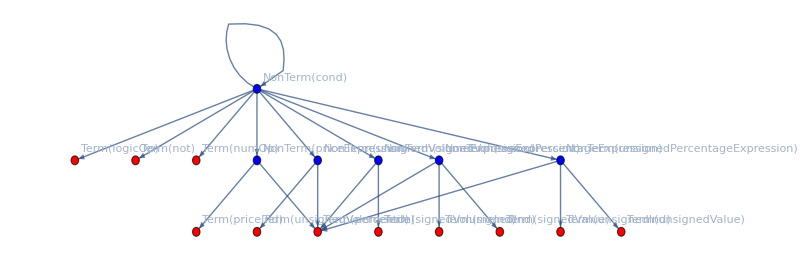

```mathematica
GrammarGraph[]
```

### Expression tree synthesization

Separate head from arguments

```mathematica
GetComponents[expr_/;Depth[expr]<3]:={expr};
GetComponents[expr_/;Depth[expr]≥3]:=Prepend[Level[expr,{1}],Head[expr]];
```

```mathematica
GetComponents[Less[ClosePrice[],Prev[3,ClosePrice[]]]]
```

{Less,ClosePrice[],Prev[3,ClosePrice[]]}

Rebuild expression from components

```mathematica
ExprFromComponents[components_ /;Length[components]≤1]:=First[components];
ExprFromComponents[components_ /;Length[components]>1]:=Block[{head,rest},
{head,rest} = {First[components],Rest[components]};
Apply[head,rest]
];
```

```mathematica
ExprFromComponents[{Less,ClosePrice[],Prev[3,ClosePrice[]]}] // FullForm
```

Less[ClosePrice[],Prev[3,ClosePrice[]]]

Find the positions of values to be synthesized on the synthesizations list

```mathematica
GetValue[treeSymbol_]:=ReplaceAll[treeSymbol,NonTerm[_,rule_]:>grammar[[rule]]["Value"]];
MatchPositions[expr_,synthesizations_]:=Block[{pos,newSynth,recursive},
pos = FirstPosition[synthesizations,First[expr]];
If[pos =!=Missing["NotFound"],
newSynth = ReplacePart[synthesizations,First[pos]->Found]
,
newSynth = synthesizations;
pos = {};
];
recursive = If[Rest[expr]≠{},MatchPositions[Rest[expr],newSynth],{}];
Transpose@{Flatten@Join[pos,recursive]}
];
```

```mathematica
grammar[[12]]
```

<|From→volumeExpression,To→{Term[lag],Term[volumeTechInd]},Value→Prev[Term[volumeTechInd][Value],Term[lag][Value]]|>

```mathematica
synthValue = GetValue[NonTerm["volumeExpression",12]]
```

Prev[Term[volumeTechInd][Value],Term[lag][Value]]

```mathematica
GetComponents[synthValue]
```

{Prev,Term[volumeTechInd][Value],Term[lag][Value]}

```mathematica
MatchPositions[GetComponents[synthValue],{Term["volumeTechInd"]["Value"],Term["lag"]["Value"]}]
```

{{1},{2}}

Synthesize the value of the current components from the list of synthValues.

```mathematica
Synthesize[exprComponents_,synthValues_]:=Block[{positions,lastPos,tmpSynthValues = synthValues,tmpExprComponents = exprComponents},
Do[
positions = Position[tmpSynthValues[[All,1]],tmpExprComponents[[i]]];
If[positions≠ {},
lastPos = First@Last@positions;
tmpExprComponents[[i]] = Replace[tmpExprComponents[[i]],Part[tmpSynthValues,lastPos]];
tmpSynthValues = Delete[tmpSynthValues,lastPos];
];
,{i,1,Length[tmpExprComponents]}
];

ExprFromComponents[tmpExprComponents]
];
```

```mathematica
GetComponents[synthValue]
```

{Prev,Term[volumeTechInd][Value],Term[lag][Value]}

```mathematica
Synthesize[
GetComponents[synthValue],
{Term["volumeTechInd"]["Value"]->"TransactionVolume[]",Term["lag"]["Value"]->"20"}
]
```

Prev[TransactionVolume[],20]

Synthesize terminals and nonterminals.

```mathematica
SynthesizeNonTerm[treeSymbol_,synthesizations_]:=Block[{val,components,eval,matchPos,newSynth,newSynthLabel},
val = GetValue[treeSymbol];
components = GetComponents[val];
matchPos = MatchPositions[components,synthesizations[[All,1]]];
eval = Synthesize[components,Extract[synthesizations,matchPos]];
newSynth = Delete[synthesizations,matchPos];
newSynthLabel = ReplaceAll[treeSymbol,NonTerm[x_,_]:>NonTerm[x]["Value"]];

Prepend[newSynth,newSynthLabel->eval]
];

SynthesizeTerm[treeSymbol_,synthesizations_]:=Block[{eval,new},
(* Label the value of a Terminal *)
If[Length[treeSymbol]==2,
Prepend[synthesizations, ReplaceAll[treeSymbol,Term[termName_,value_]:>(Term[termName]["Value"]->value)]],
synthesizations
]
];
```

Complete tree synthesization.

```mathematica
SynthesizeTree[graph_,labels_]:=Block[{depthFirstScan,labeledDFS,symbolType,synthesized},
(* Walk the parse tree in post order *)
depthFirstScan = First@Last@Reap[
DepthFirstScan[graph,1,{"PostvisitVertex"->(Sow[#]&)}]
];
labeledDFS = depthFirstScan /.labels;

(* Synthesize in the order of the depthfirstscan *)
synthesized={};
Do[
symbolType = Head[s];
If[symbolType === Term,synthesized = SynthesizeTerm[s,synthesized]];
If[symbolType === NonTerm,synthesized = SynthesizeNonTerm[s,synthesized]];
,
{s,labeledDFS}
];

ToExpression[ToString[synthesized[[1,-1]]]]
];
SynthesizeTree[{graph_,labels_}]:=SynthesizeTree[graph,labels];
```

## Operations over trees

### Implementation:

Tree manipulations operations.

```mathematica
RestartLabelsAt[graph_,labels_,startNum_ : 1]:=Block[{replaceRules,newEdges,newLabels},
replaceRules = Thread[VertexList[graph]->Range[startNum,startNum+Length[VertexList[graph]]-1]];
newEdges = EdgeList[graph]/.replaceRules;
newLabels = MapAt[#/.replaceRules&,labels,{All,1}];

{Graph[newEdges,VertexLabels->newLabels,ImageSize->500],newLabels}
];
Subtree[graph_,labels_,vertex_]:=Block[{children,toDelete,subtree,sublabels},
children = First@Last@Reap@DepthFirstScan[graph,vertex,{"PrevisitVertex"->(Sow[#]&)}];
toDelete = Complement[VertexList[graph],children];
subtree = VertexDelete[graph,Complement[VertexList[graph],children]];
sublabels = Cases[labels,x_/;MemberQ[children,First[x]]];

{subtree,sublabels}
];
DeleteSubtree[graph_,labels_,vertex_]:=Block[{subtree,sublabels,subVertexes,conectionRemoved,withoutSubtree,newLabels},
{subtree,sublabels} = Subtree[graph, labels, vertex];
subVertexes = VertexList[subtree];
conectionRemoved = ReplaceAll[EdgeList[graph],((x_/;!MemberQ[subVertexes,x])->(y_/;MemberQ[subVertexes,y])):>x->Empty];
withoutSubtree = If[Length[Intersection[VertexList[conectionRemoved],subVertexes]]≠ 0,
VertexDelete[conectionRemoved,subVertexes],
conectionRemoved
];
newLabels = Complement[labels,sublabels];

{Graph[withoutSubtree,VertexLabels->newLabels,ImageSize->500],newLabels}
];

InsertSubtree[graph_,labels_,subtree_,sublabels_]:=Block[{missingVertexes,edges,missing,splitPos,left,right,middleRules,formattedSubtreeRoot,remaining,rightRules,newLeftGraph,newMiddleGraph,newRightGraph,insertLabels,incompleteLabels,newEdges,newLabels,newRootForSub,newRightLabels},
If[!MemberQ[VertexList[graph],Empty],Return[$Failed]];

edges = DeleteCases[VertexList[graph],Empty];
missingVertexes = Complement[Range[Max[edges]],edges];
If[missingVertexes ≠ {},
missing =  First@missingVertexes;
splitPos = First@FirstPosition[EdgeList[graph],_->Empty];
{left,right} = TakeDrop[EdgeList[graph],splitPos];

middleRules = Thread[VertexList[subtree]->(VertexList[subtree]+missing-1)];
newMiddleGraph = EdgeList[subtree]/.middleRules;
formattedSubtreeRoot = 1 /.middleRules;

remaining = Complement[VertexList[right],VertexList[left]];
rightRules = Thread[remaining->(remaining+Max[VertexList[newMiddleGraph]]-Min[remaining]+1)];

newLeftGraph = left/.Empty->formattedSubtreeRoot;
newRightGraph = right /.rightRules;
insertLabels = MapAt[#/.middleRules&,sublabels,{All,1}];
incompleteLabels = MapAt[#/.rightRules&,labels,{All,1}];

newEdges = Join[newLeftGraph,newMiddleGraph,newRightGraph];
newLabels = SortBy[Join[incompleteLabels,insertLabels],First];

,

newRootForSub = Max[DeleteCases[VertexList[graph],Empty]]+1;
{newRightGraph,newRightLabels} = RestartLabelsAt[subtree,sublabels,newRootForSub];
newEdges = Join[EdgeList[graph]/.Empty->newRootForSub,EdgeList[newRightGraph]];
newLabels = Join[labels,newRightLabels];
];

{Graph[newEdges,VertexLabels->newLabels,ImageSize->500],newLabels}
];
```

### Examples:

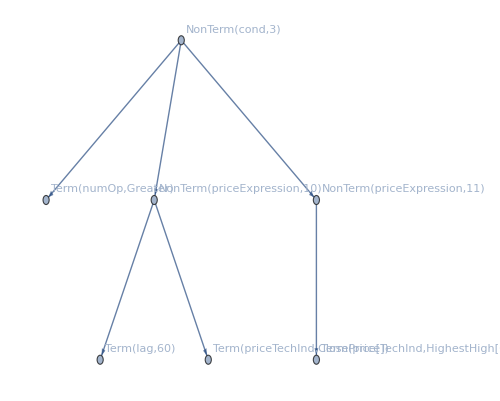
```mathematica
{g1,labels1} = {-Graphics-,{1->NonTerm["cond",3],2->Term["numOp","Greater"],3->NonTerm["priceExpression",10],4->Term["lag","60"],5->Term["priceTechInd","ClosePrice[]"],6->NonTerm["priceExpression",11],7->Term["priceTechInd","HighestHigh[60]"]}};
```

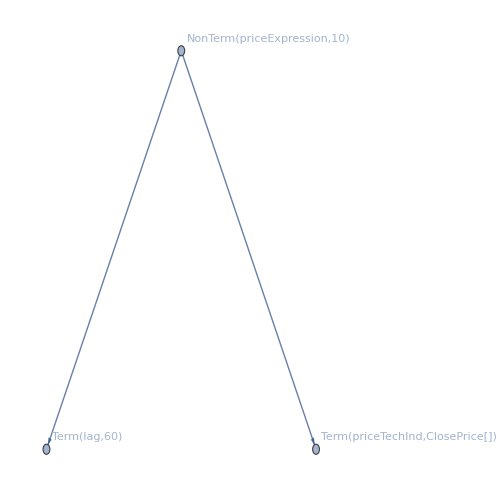
{-Graphics-,{1→NonTerm[priceExpression,10],2→Term[lag,60],3→Term[priceTechInd,ClosePrice[]]}}

```mathematica
subtree1 = Apply[RestartLabelsAt,Subtree[g1,labels1,3]]
```

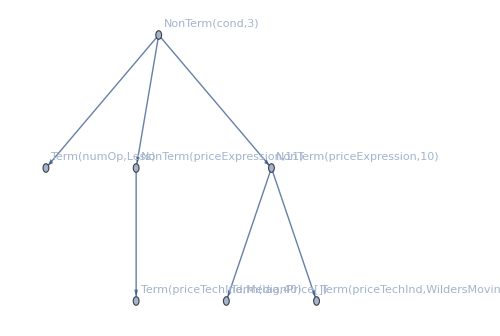
```mathematica
{g2,labels2} = {-Graphics-,{1->NonTerm["cond",3],2->Term["numOp","Less"],3->NonTerm["priceExpression",11],4->Term["priceTechInd","MedianPrice[]"],5->NonTerm["priceExpression",10],6->Term["lag","40"],7->Term["priceTechInd","WildersMovingAverage[60]"]}};
```

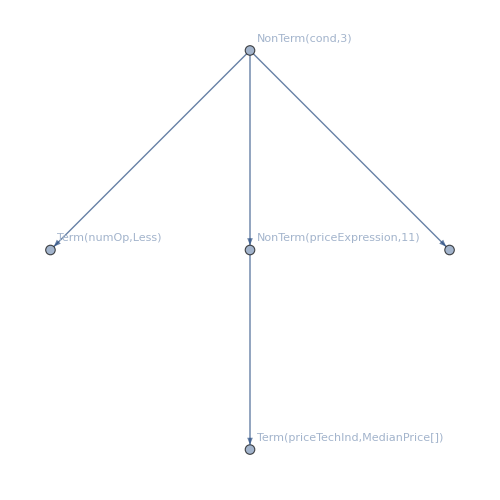
{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,Less],3→NonTerm[priceExpression,11],4→Term[priceTechInd,MedianPrice[]]}}

```mathematica
cropped2 = DeleteSubtree[g2,labels2,5]
```

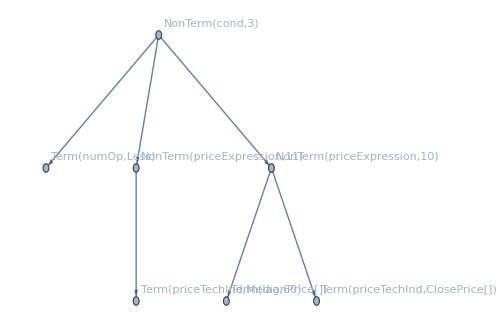
{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,Less],3→NonTerm[priceExpression,11],4→Term[priceTechInd,MedianPrice[]],5→NonTerm[priceExpression,10],6→Term[lag,60],7→Term[priceTechInd,ClosePrice[]]}}

```mathematica
inserted = InsertSubtree[First[cropped2],Last[cropped2],First[subtree1],Last[subtree1]]
```

```mathematica
SynthesizeTree[First[inserted],Last[inserted],grammar] // FullForm
```

Less[MedianPrice[],Prev[ClosePrice[],60]]

## Random function generation

### Implementation:

```mathematica
NonTermName[nonterm_]:=ReplaceAll[nonterm,NonTerm[x_]:>x];
NonTermWithProd[nonterm_,prodIndex_]:=NonTerm[NonTermName[nonterm],prodIndex];
ApplicableProductions[nonterm_]:=First@Transpose@Position[grammar,KeyValuePattern["From"->NonTermName[nonterm]]];
UnassignedProductionQ[prod_]:=MatchQ[prod,NonTerm[_]];

ProductionRuleAsGraph[prodIndex_]:=Block[{rootNonTerm,newLeafs,edgeList,vertexLabels},
rootNonTerm = NonTermWithProd[NonTerm[grammar[[prodIndex]]["From"]],prodIndex];
newLeafs = grammar[[prodIndex]]["To"];
edgeList = Thread[1->Range[2,1+Length[newLeafs]]];
vertexLabels = Prepend[Thread[Range[2,1+Length[newLeafs]]->newLeafs],1->rootNonTerm];

{Graph[edgeList,VertexLabels->vertexLabels],vertexLabels}
];

GrowTree[graph_,labels_,maxDepth_]:=Block[{unassignedVertexes,replaceIndex,cropped,replaceNonTerm,selectedProduction,sub,new},
If[graph===$Failed || labels ===$Failed,Return[{$Failed,$Failed}]];

unassignedVertexes = Cases[labels,HoldPattern[v_->t_ /; UnassignedProductionQ[t]]:>v];
replaceIndex = RandomChoice[unassignedVertexes];
cropped = DeleteSubtree[graph,labels,replaceIndex];
replaceNonTerm = Last[labels[[replaceIndex]]];
selectedProduction = RandomChoice[ApplicableProductions[replaceNonTerm]];
sub = ProductionRuleAsGraph[selectedProduction];
new = InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub]];

If[Length[Last[new]]<maxDepth,new,{$Failed,$Failed}]
];

grammarRootNonTerm = First[grammar]["From"];
grammarRootIndexes = Count[grammar,KeyValuePattern["From"->grammarRootNonTerm]];

GenerateRandomTree[maxDepth_]:=Block[{tree},
tree =ProductionRuleAsGraph[RandomInteger[{1,grammarRootIndexes}]];
NestWhile[
GrowTree[First[#],Last[#],maxDepth]&,tree,#=!={$Failed,$Failed}&&Apply[Or,Map[UnassignedProductionQ,Cases[Last[#][[All,2]],_NonTerm]]]&
]
];
RandomTerm[name_,terminalSet_]:=RandomChoice[Cases[terminalSet,Term[name,_]]];
GenerateRandomTerminals[labels_]:=ReplaceAll[labels,HoldPattern[v_->Term[n_]]:>(v->RandomTerm[n,terminalSet])];

GenerateRandomFunction[maxDepth_]:=Block[{g=$Failed,l=$Failed,labelsWithTerminals,sg,sl,synth},
While[g===$Failed || l ===$Failed,
{g,l} = GenerateRandomTree[maxDepth];
];
labelsWithTerminals = GenerateRandomTerminals[l];

{sg,sl} = {Graph[EdgeList[g],VertexLabels->labelsWithTerminals,ImageSize->500],labelsWithTerminals};

synth = ReplaceAll[SynthesizeTree[sg,sl],grammarAxioms];

If[synth===True||synth===False,
Return[GenerateRandomFunction[maxDepth]];
,
Return[{sg,sl}];
];
];

SynthesizeFunction[{graph_,labels_}]:=SynthesizeTree[{graph,labels}];
SynthesizeFunction[graph_,labels_]:=SynthesizeTree[graph,labels];
GenerateRandomStrategy[maxDepth_]:=SynthesizeFunction[GenerateRandomFunction[maxDepth]];
```

### Example:

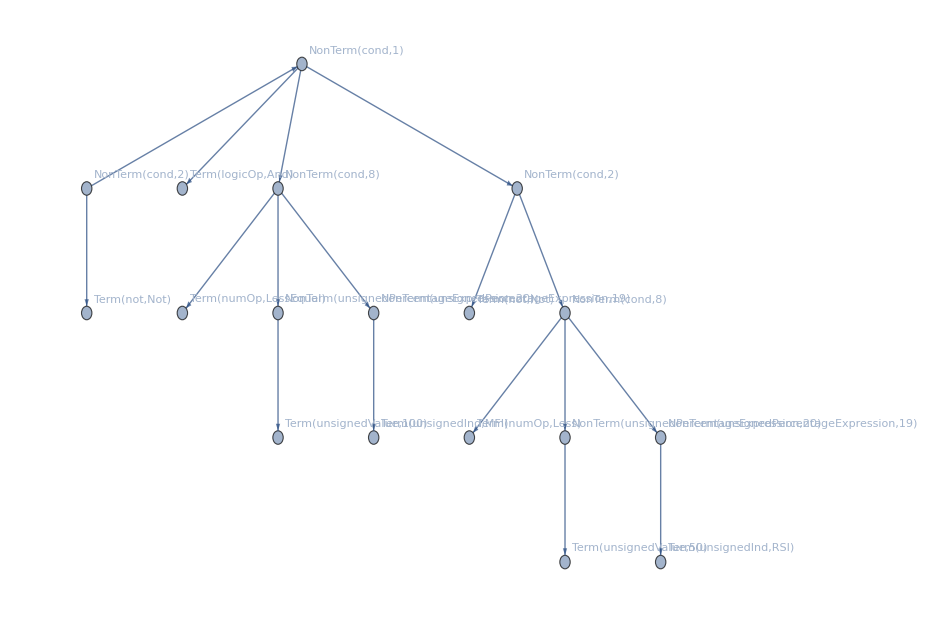
{-Graphics-,{1→NonTerm[cond,2],2→Term[not,Not],3→NonTerm[cond,1],4→Term[logicOp,And],5→NonTerm[cond,8],6→Term[numOp,LessEqual],7→NonTerm[unsignedPercentageExpression,20],8→Term[unsignedValue,100],9→NonTerm[unsignedPercentageExpression,19],10→Term[unsignedInd,MFI],11→NonTerm[cond,2],12→Term[not,Not],13→NonTerm[cond,8],14→Term[numOp,Less],15→NonTerm[unsignedPercentageExpression,20],16→Term[unsignedValue,50],17→NonTerm[unsignedPercentageExpression,19],18→Term[unsignedInd,RSI]}}

!(100≤Indicator[MFI,stock,time]&&50≥Indicator[RSI,stock,time])

```mathematica
{g,l} = GenerateRandomFunction[500]
SynthesizeTree[g,l]
```

```mathematica
100≤Indicator[MFI,stock,time]
```

```mathematica
First@Timing[
Block[{g,l},Table[
{g,l} = GenerateRandomFunction[500];
SynthesizeTree[g,l],
10000]
]
]
```

47.9531

```mathematica
tenStrategies = Table[GenerateRandomStrategy[1000],10];
Column@Table[GenerateRandomStrategy[1000],10]
```

IndQuantile[ClosingBias,0.85,stock,time]>IndQuantile[MFI,0.75,stock,time]
Indicator[PricePercentangeChangeOpenToClose,stock,time]≤IndQuantile[PricePercentangeChangeOpenToClose,0.05,stock,time]
IndQuantile[ClosingBias,0.05,stock,time]≤IndQuantile[RSI,0.85,stock,time]
IndQuantile[ExtensionRatio,0.15,stock,time]≥Indicator[ExtensionRatio,stock,time]
IndQuantile[TradingVolume,0.05,stock,time]<Indicator[TradingVolume,stock,time]
IndQuantile[TradingVolume,0.75,stock,time]≥Indicator[TradingVolume,stock,time]
IndQuantile[TradingVolume,0.75,stock,time]≥Indicator[TradingVolume,stock,time]||IndQuantile[PricePercentangeChangeOpenToClose,0.75,stock,time]<Indicator[PricePercentangeChangeOpenToClose,stock,time]
IndQuantile[OBV,0.95,stock,time]<Indicator[OBV,stock,time]&&IndQuantile[MFI,0.95,stock,time]≥Indicator[ClosingBias,stock,time]
Indicator[OBV,stock,time]≤IndQuantile[OBV,0.15,stock,time]
Indicator[RSI,stock,time]≥Indicator[MFI,stock,time]

```mathematica
ConvertStrategyFunctionToCpp[(IndQuantile[ClosingBias,0.95,stock,time]≤Indicator[ClosingBias,stock,time]&&Indicator[PricePercentangeChangeOpenToClose,stock,time]>IndQuantile[ExtensionRatio,0.05,stock,time])||Indicator[TypicalPrice,stock,time]<IndQuantile[MedianPrice,0.85,stock,time]]
```

(IndQuantile("ClosingBias",0.95,stock,time)<=Indicator("ClosingBias",stock,time)&&Indicator("PricePercentangeChangeOpenToClose",stock,time)>IndQuantile("ExtensionRatio",0.05,stock,time))||Indicator("TypicalPrice",stock,time)<IndQuantile("MedianPrice",0.85,stock,time)

## Crossover

Crossover operator that selects NonTerms that are common in both parents and swaps them.

### Implementation:

```mathematica
Crossover[graph1_,labels1_,graph2_,labels2_]:=Block[{nonterms1,nonterms2,commonNonTerms,matchsIn1,vertex1,vertex1NonTerm,vertex2,cropped,sub},
nonterms1 = Cases[labels1[[All,2]],_NonTerm];
nonterms2 = Cases[labels2[[All,2]],_NonTerm];
commonNonTerms = Intersection[nonterms1,nonterms2];

matchsIn1 = Cases[labels1,HoldPattern[v_->l_/;MemberQ[commonNonTerms,l]]:>{v,l}];
If[Length[matchsIn1]<2,Return[RandomChoice[{{graph1,labels1},{graph2,labels2}}]]];

{vertex1,vertex1NonTerm} = RandomChoice[Drop[matchsIn1,1]];
vertex2 = RandomChoice[Cases[labels2,HoldPattern[v_->l_/;l==vertex1NonTerm]:>v]];
cropped = DeleteSubtree[graph1,labels1,vertex1];
sub = Apply[RestartLabelsAt,Subtree[graph2,labels2,vertex2]];

InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub]]
];
CoupleCrossover[ind1_,ind2_]:=Block[{childGenome},
childGenome = Crossover[First[ind1["Genome"]],Last[ind1["Genome"]],First[ind2["Genome"]],Last[ind2["Genome"]]];
<|"Genome"->childGenome,"Profit"->Null|>
];
PopulationCrossover[population_,childrenPerCouple_]:=Block[{parts},
parts = Partition[RandomSample[population],2];
Apply[Join,Table[Map[Apply[CoupleCrossover,#]&,parts],childrenPerCouple]]
];
```

### Examples:

```mathematica
{g1,l1} = GenerateRandomFunction[500];
{g2,l2} = GenerateRandomFunction[500];
SynthesizeTree[g1,l1]
SynthesizeTree[g2,l2]
```

IndQuantile[EMA,0.15,stock,time]<IndQuantile[TypicalPrice,0.25,stock,time]

Indicator[HighPrice,stock,time]≥Indicator[EMA,stock,time]

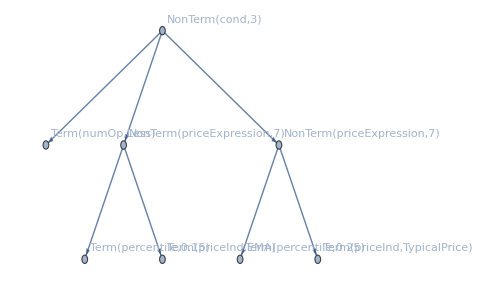
{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,Less],3→NonTerm[priceExpression,7],4→Term[percentile,0.15],5→Term[priceInd,EMA],6→NonTerm[priceExpression,7],7→Term[percentile,0.25],8→Term[priceInd,TypicalPrice]}}

IndQuantile[EMA,0.15,stock,time]<IndQuantile[TypicalPrice,0.25,stock,time]

```mathematica
{childg,childl} = Crossover[g1,l1,g2,l2]
SynthesizeTree[childg,childl]
```

```mathematica
SynthesizeTree[Crossover[g1,l1,g2,l2]]
```

Indicator[HighPrice,stock,time]≥Indicator[EMA,stock,time]

```mathematica
uniqueChilds = DeleteDuplicates[ProgressTable[SynthesizeTree[Crossover[g1,l1,g2,l2]],1000]];
```

```mathematica
uniqueChilds
```

{IndQuantile[EMA,0.15,stock,time]<IndQuantile[TypicalPrice,0.25,stock,time],Indicator[HighPrice,stock,time]≥Indicator[EMA,stock,time]}

## Mutation

### Implementation:

```mathematica
SwapNonTerms[graph_,labels_]:=Block[{nonterms,swapableNonTerms,vertex1,vertex2,sub1,sub2,cropped1,tempG,tempL,cropped2},
nonterms = Cases[labels,HoldPattern[v_->l_NonTerm]:>{v,l}];
swapableNonTerms = Select[GatherBy[Drop[nonterms,1],First[Level[Last[#],{1}]]&],Length[#]>1&];
If[swapableNonTerms=={},Return[{graph,labels}]];

{vertex1,vertex2} = SortBy[RandomSample[First[RandomChoice[swapableNonTerms,1]],2],First][[All,1]];

sub1 = Apply[RestartLabelsAt,Subtree[graph,labels,vertex1]];
sub2 = Apply[RestartLabelsAt,Subtree[graph,labels,vertex2]];

cropped1 = DeleteSubtree[graph,labels,vertex2];
{tempG,tempL} = InsertSubtree[First[cropped1],Last[cropped1],First[sub1],Last[sub1]];
cropped2= DeleteSubtree[tempG,tempL,vertex1];

InsertSubtree[First[cropped2],Last[cropped2],First[sub2],Last[sub2]]
];
```

```mathematica
TreeMutation[graph_,labels_]:=SwapNonTerms[graph,labels];

uniqueTerms = {"not","volumeTechInd"};
TerminalMutation[labels_]:=Block[{mutableTerms,choice,type,newTerm,availableTerms},
mutableTerms = DeleteCases[labels,HoldPattern[_->Term[x_,_]/;MemberQ[uniqueTerms,x]]];
choice = RandomChoice[Cases[mutableTerms,HoldPattern[_->_Term]]];
type = First[Level[Last[choice],{1}]];
availableTerms = Complement[Cases[terminalSet,Term[type,_]],{Last[choice]}];

If[availableTerms ≠ {},
newTerm = RandomChoice[availableTerms];
ReplacePart[labels,First[choice]->(First[choice]->newTerm)]
,
labels
]
];
Mutation[graph_,labels_]:=Block[{mutatedSymbols,treeMutation},
If[RandomReal[]≥0.5,
treeMutation = TreeMutation[graph,labels];

(* If tree mutation doesn't change anything, mutate the terminals *)
If[treeMutation != {graph,labels},
Return[treeMutation];
,
mutatedSymbols = TerminalMutation[labels];
Return[{Graph[EdgeList[graph],VertexLabels->mutatedSymbols,ImageSize->500],mutatedSymbols}]
];

,
mutatedSymbols = TerminalMutation[labels];
Return[{Graph[EdgeList[graph],VertexLabels->mutatedSymbols,ImageSize->500],mutatedSymbols}]
]
];
MutateIndividual[ind_]:=<|"Genome"->Mutation[First[ind["Genome"]],Last[ind["Genome"]]],"Profit"->Null|>;
PopulationMutate[population_,probability_]:=Map[If[RandomReal[]≤probability,MutateIndividual[#],#]&,population];
```

### Example:

```mathematica
{g,l}= GenerateRandomFunction[500];
SynthesizeTree[g,l]
```

TradingVolume[#stock,#time]≤IndQuantile[TradingVolume[#stock,#time],0.05]

```mathematica
{mutatedTree,mutatedLabels} = Mutation[g,l];
SynthesizeTree[mutatedTree,mutatedLabels]
```

TradingVolume[#stock,#time]≤IndQuantile[TradingVolume[#stock,#time],0.15]

## Backtester implementation

### Load Backtester link:

```mathematica
If[$OperatingSystem=="Windows",
link = Install[FileNameJoin[{NotebookDirectory[],"TradingStrategyBacktester","Backtester","x64","Mathematica","Backtester.exe"}]]
,
link = Install[FileNameJoin[{NotebookDirectory[],"TradingStrategyBacktester","Build","Backtester"}]]
]
```

LinkObject[…]

#### Debug

```mathematica
linkObject = LinkConnect["gatillo"]
link = Install[linkObject]
```

LinkObject[…]

LinkObject[…]

#### Defined functions

```mathematica
Column@LinkPatterns[link]
```

BTLoadDataset[path_String,identifier_String]
BTUnloadDataset[identifier_String]
BTSwitchToDataset[identifier_String]
BTGetNumberOfLoadedStocks[]
BTGetStockNamesOfDataset[]
BTGetDate[stock_String,time_Integer]
BTGetDates[stock_String]
BTGetIndicator[indicator_String,stock_String,time_Integer]
BTGetIndicatorTimeSeries[indicator_String,stock_String]
BTGetQuantileIndicator[indicator_String,percentile_String,stock_String,time_Integer]
BTGetQuantileIndicatorTimeSeries[indicator_String,percentile_String,stock_String]
BTGetStrategyValues[strategy_String,stock_String]
BTGetStrategyExecutionDataStoplossProfitTake[strategy_String,stock_String,profitTake_Real,stopLoss_Real,transactionCost_Real]
BTGetStrategyExecutionDataTimestopHit[strategy_String,stock_String,timePeriod_Integer,transactionCost_Real]
BTGetStrategyExecutionDataMarketTiming[strategy_String,stock_String,transactionCost_Real]
BTGetStrategyReturnsStoplossProfitTake[returnType_String,strategy_String,stock_String,profitTake_Real,stopLoss_Real,transactionCost_Real,minibatchSize_Integer:-1]
BTGetStrategyReturnsTimestopHit[returnType_String,strategy_String,stock_String,timePeriod_Integer,transactionCost_Real,minibatchSize_Integer:-1]
BTGetStrategyReturnsMarketTiming[returnType_String,strategy_String,stock_String,transactionCost_Real,minibatchSize_Integer:-1]
BTGetStrategyReturnsAllStocksStoplossProfitTake[returnType_String,strategy_String,profitTake_Real,stopLoss_Real,transactionCost_Real,minibatchSize_Integer:-1]
BTGetStrategyReturnsAllStocksTimestopHit[returnType_String,strategy_String,timePeriod_Integer,transactionCost_Real,minibatchSize_Integer:-1]
BTGetStrategyReturnsAllStocksMarketTiming[returnType_String,strategy_String,transactionCost_Real,minibatchSize_Integer:-1]
BTStrategyCompilationInfo[strategy_String]

```mathematica
BTGetStrategyReturnsStoplossProfitTake[returnType_String,strategy_String,stock_String,profitTake_Real,stopLoss_Real,transactionCost_Real,minibatchSize_Integer:-1]
```

```mathematica
BTGetStrategyReturnsAllStocksStoplossProfitTake[returnType_String,strategy_String,profitTake_Real,stopLoss_Real,transactionCost_Real,minibatchSize_Integer:-1]
```

```mathematica
trainingDatasetDirectory = FileNameJoin[{NotebookDirectory[],"SP500ByStock","UtilitiesRegulatedElectric","Training"}];
BTLoadDataset[trainingDatasetDirectory,"TrainingSet"]
```

True

```mathematica
validationDatasetDirectory = FileNameJoin[{NotebookDirectory[],"SP500ByStock","UtilitiesRegulatedElectric","Validation"}];
BTLoadDataset[validationDatasetDirectory,"ValidationSet"]
```

True

```mathematica
testingDatasetDirectory = FileNameJoin[{NotebookDirectory[],"SP500Testing"}];
BTLoadDataset[testingDatasetDirectory,"TestingSet"]
```

True

```mathematica
BTSwitchToDataset["TrainingSet"];
```

```mathematica
Length@BTGetDates["AAPL"]
```

8780

```mathematica
BTSwitchToDataset["ValidationSet"];
```

```mathematica
Length@BTGetDates["AAPL"]
```

1924

```mathematica
totalStocks = BTGetNumberOfLoadedStocks[]
```

20

```mathematica
stockNames = BTGetStockNamesOfDataset[]
```

{AEE,AEP,CMS,CNP,D,DTE,DUK,ED,EIX,ES,ETR,EVRG,FE,LNT,NEE,PNW,PPL,SO,WEC,XEL}

### Convenience functions:

```mathematica
Multiply[list_List]:=Apply[Times,list];
CondenseDivReturns[profit_Association]:=Mean[Map[Multiply,Values[profit]]];
CondenseReturns[profit_Association]:=Total[Map[Total,Values[profit]]];

(* Aliases *)
BTGetNumberOfDates[ticker_]:=Length[BTGetDates[ticker]];
```

### Examples:

```mathematica
pProfitTake = 0.5;
pLossExit = -0.5;
```

```mathematica
{g,l}= GenerateRandomFunction[500];
strategyFunction = ConvertStrategyFunctionToCpp[SynthesizeTree[g,l]]
```

IndQuantile("TradingVolume","0.15",stock,time)<=Indicator("TradingVolume",stock,time)&&IndQuantile("ExtensionRatio","0.85",stock,time)>=IndQuantile("PricePercentangeChangeOpenToClose","0.75",stock,time)&&Indicator("TradingVolume",stock,time)>=IndQuantile("TradingVolume","0.25",stock,time)

```mathematica
myStrategy = "Indicator(\"EMA\",stock,time)<Indicator(\"ClosePrice\",stock,time)";
```

```mathematica
BTStrategyCompilationInfo[myStrategy]
```

The strategy program is OK.

```mathematica
BTGetStrategyExecutionDataStoplossProfitTake[myStrategy,"AAPL",pProfitTake,pLossExit,0.0025]
```

{<|Signal→Buy,Time→"2008-03-11",TimeIndex→8,Price→4.54821|>,<|Signal→Sell,Time→"2009-10-20",TimeIndex→415,Price→7.09857|>,<|Signal→Buy,Time→"2009-10-21",TimeIndex→416,Price→7.31857|>,<|Signal→Sell,Time→"2010-10-15",TimeIndex→664,Price→11.2407|>,<|Signal→Buy,Time→"2010-10-18",TimeIndex→665,Price→11.3571|>,<|Signal→Sell,Time→"2012-02-09",TimeIndex→996,Price→17.6132|>,<|Signal→Buy,Time→"2012-02-10",TimeIndex→997,Price→17.6221|>,<|Signal→Sell,Time→"2014-10-28",TimeIndex→1679,Price→26.685|>,<|Signal→Buy,Time→"2014-10-29",TimeIndex→1680,Price→26.835|>,<|Signal→Sell,Time→"2017-08-29",TimeIndex→2393,Price→40.7275|>,<|Signal→Buy,Time→"2017-08-30",TimeIndex→2394,Price→40.8375|>,<|Signal→Sell,Time→"2019-10-25",TimeIndex→2936,Price→61.645|>,<|Signal→Buy,Time→"2019-10-28",TimeIndex→2937,Price→62.2625|>,<|Signal→Sell,Time→"2020-07-08",TimeIndex→3111,Price→95.3425|>,<|Signal→Buy,Time→"2020-07-09",TimeIndex→3112,Price→95.7525|>,<|Signal→Sell,Time→"2021-05-06",TimeIndex→3320,Price→129.74|>}

```mathematica
Total@BTGetStrategyReturnsStoplossProfitTake["SimpleReturns",myStrategy,"AAPL",pProfitTake,pLossExit,0.0025]
```

123.559

```mathematica
BTGetStrategyReturnsStoplossProfitTake["DivReturns",myStrategy,"AAPL",pProfitTake,pLossExit,0.0025]
```

{1.56074,1.53592,1.55085,1.51429,1.5177,1.50952,1.5313,1.35495}

```mathematica
Total@BTGetStrategyReturnsMarketTiming["SimpleReturns",myStrategy,"AAPL",0.0025]
```

89.1308

```mathematica
BTGetStrategyReturnsAllStocksStoplossProfitTake["DivReturns",myStrategy,pProfitTake,pLossExit,0.0025]
```

<|AAPL→{1.56074,1.53592,1.55085,1.51429,1.5177,1.50952,1.5313,1.35495},ZION→{0.397382,1.59844,0.498012,0.484692,1.61323,1.51498,1.54105,1.51095,0.48538,1.64776,1.18384}|>

```mathematica
CondenseProfit[BTGetStrategyReturnsAllStocksStoplossProfitTake["DivReturns",myStrategy,pProfitTake,pLossExit,0.0025]]
```

13.793

```mathematica
?CondenseProfit
```

### Random strategies statistic:

```mathematica
RandomStrategyReturnsStoplossProfitTake[returnType_, profitTake_,stopLoss_,transactionCost_Real]:=Block[{g,l,strategyFunction,trainingSetResult,validationSetResult},
{g,l}= GenerateRandomFunction[1000];
strategyFunction = ConvertStrategyFunctionToCpp[SynthesizeTree[g,l]];

BTSwitchToDataset["TrainingSet"];
trainingSetResult = BTGetStrategyReturnsAllStocksStoplossProfitTake[returnType,strategyFunction,profitTake,stopLoss,transactionCost];

BTSwitchToDataset["ValidationSet"];
validationSetResult = BTGetStrategyReturnsAllStocksStoplossProfitTake[returnType,strategyFunction,profitTake,stopLoss,transactionCost];

If[returnType == "DivReturns",
{CondenseDivReturns[trainingSetResult],CondenseDivReturns[validationSetResult]},
{CondenseReturns[trainingSetResult],CondenseReturns[validationSetResult]}
]
];
ScatterPlotCorrelation[data_]:=Apply[Correlation,Transpose[data]];
```

```mathematica
randomReturns = ProgressTable[{profitTake,stopLoss,ScatterPlotCorrelation[ProgressTable[RandomStrategyReturnsStoplossProfitTake["DivReturns", profitTake,stopLoss,0.0005],500]]},{profitTake,0.001,0.01,0.001},{stopLoss,-0.001,-0.01,-0.001}];
```

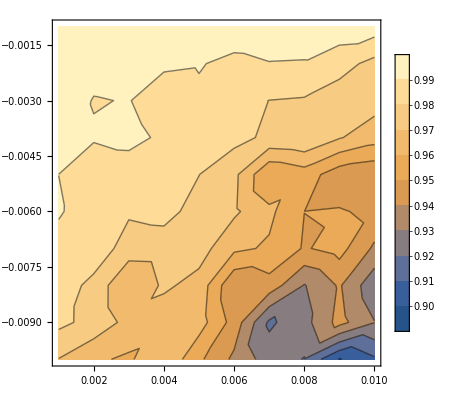

```mathematica
ListContourPlot[Flatten[randomReturns,1],
PlotRange->All,
PlotLegends->Automatic]
```

```mathematica
RandomStrategyReturnsStoplossProfitTake["DivReturns",0.01,-0.01,0.0005]
```

0.946634

```mathematica
profitTake
```

0.1

```mathematica
Clear[profitTake]
```

```mathematica
returnsByExit = ProgressTable[{profitTake,lossExit,Mean@Table[RandomStrategyReturnsStoplossProfitTake["DivReturns", profitTake,lossExit,0.0005],50]},{profitTake,0.01,0.05,0.0025},{lossExit,-0.01,-0.05,-0.0025}];
```

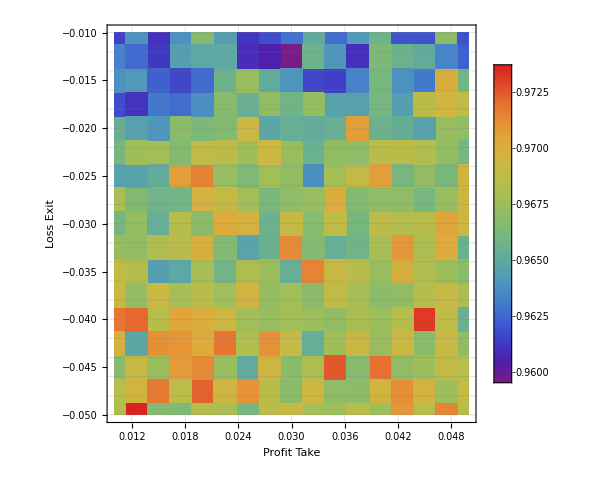

```mathematica
ListDensityPlot[Flatten[returnsByExit,1],
PlotLegends->Automatic,
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameLabel->{Style["Profit Take",15], Style["Loss Exit",15]},
ColorFunction->"Rainbow",
InterpolationOrder->0
]
```

```mathematica
returnsDispByExit = ProgressTable[{profitTake,lossExit,StandardDeviation@Table[RandomStrategyReturnsStoplossProfitTake["DivReturns", profitTake,lossExit,0.0005],50]},{profitTake,0.01,0.05,0.0025},{lossExit,-0.01,-0.05,-0.0025}];
```

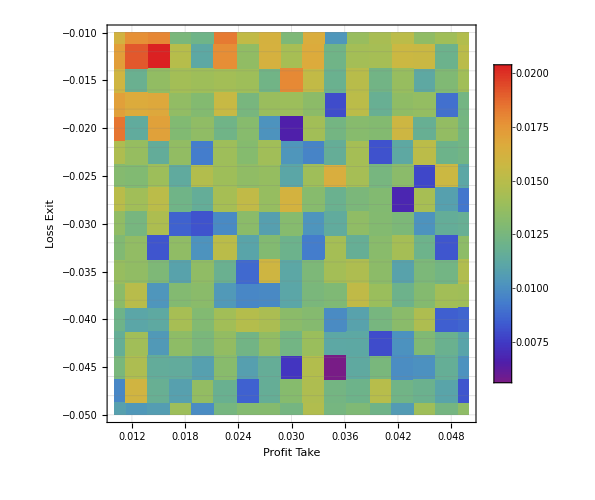

```mathematica
ListDensityPlot[Flatten[returnsDispByExit,1],
PlotLegends->Automatic,
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome",
BaseStyle->FontSize->14,
ImageSize->500,
GridLines->{Automatic,All},
GridLinesStyle->Directive[Gray,Opacity[0.3]],
FrameLabel->{Style["Profit Take",15], Style["Loss Exit",15]},
ColorFunction->"Rainbow",
InterpolationOrder->0
]
```

### Comparison of random strategies returns with Buy & Hold

```mathematica
BuyAndHoldReturn[ticker_,transactionCost_]:=(BTGetIndicator["ClosePrice",ticker,BTGetNumberOfDates[ticker]-1](1-transactionCost))/(BTGetIndicator["ClosePrice",ticker,0](1+transactionCost));
```

```mathematica
BTSwitchToDataset["TrainingSet"];
bAndhAvgRetTraining = Mean[ProgressMap[BuyAndHoldReturn[#,0.0005]&,stockNames]]
```

0.965256

```mathematica
BTSwitchToDataset["ValidationSet"];
bAndhAvgRetValidation = Mean[ProgressMap[BuyAndHoldReturn[#,0.0005]&,stockNames]]
BTSwitchToDataset["TrainingSet"];
```

0.977609

```mathematica
BTSwitchToDataset["TestingSet"];
bAndhAvgRetTesting = Mean[ProgressMap[BuyAndHoldReturn[#,0.0025]&,stockNames]]
BTSwitchToDataset["TrainingSet"];
```

1.03942

```mathematica
BTSwitchToDataset["CompleteSet"];
bAndhAvgRetComplete = Mean[ProgressMap[BuyAndHoldReturn[#,0.0025]&,stockNames]]
BTSwitchToDataset["TrainingSet"];
```

0.940514

## Fitness function

### Implementation:

```mathematica
EvaluateIndividual[individual_,profitTake_,stopLoss_,transactionCost_,dataSet_]:=Block[{indAsFunction,profit},
BTSwitchToDataset[dataSet];
indAsFunction = ConvertStrategyFunctionToCpp[SynthesizeTree[individual["Genome"]]];
profit = CondenseDivReturns[BTGetStrategyReturnsAllStocksStoplossProfitTake["DivReturns",indAsFunction,profitTake,stopLoss,transactionCost]];

<|
"Genome"->individual["Genome"],
"Profit"->profit
|>
];
EvaluatePopulation[population_,profitTake_Real,stopLoss_Real,transactionCost_,dataSet_]:=Block[{profit,populationAsFunctions},
BTSwitchToDataset[dataSet];
populationAsFunctions = Map[ConvertStrategyFunctionToCpp[SynthesizeTree[#]]&,population[[All,"Genome"]]];
profit = ProgressMapThread[CondenseDivReturns[BTGetStrategyReturnsAllStocksStoplossProfitTake["DivReturns",#1,profitTake,stopLoss,transactionCost]]&,{populationAsFunctions,population[[All,"ExitConditions"]]},"Label"-> "Backtesting "<>dataSet];

MapThread[
<|
"Genome"->#1["Genome"],
"Profit"->#2
|>&,
{population,profit}
]
];
```

### Example:

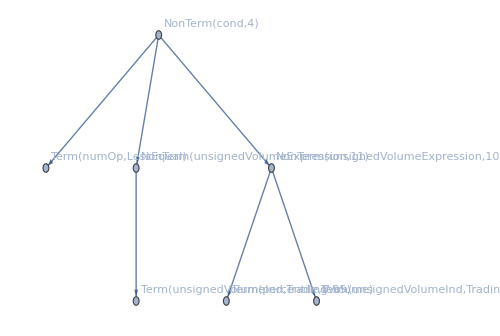
<|Genome→{-Graphics-,{1→NonTerm[cond,4],2→Term[numOp,LessEqual],3→NonTerm[unsignedVolumeExpression,11],4→Term[unsignedVolumeInd,TradingVolume],5→NonTerm[unsignedVolumeExpression,10],6→Term[percentile,0.95],7→Term[unsignedVolumeInd,TradingVolume]}},Profit→1.98151|>

```mathematica
individual = GenerateRandomIndividual[500];
EvaluateIndividual[individual,0.3,-0.3,0.0025,"TrainingSet"]
```

```mathematica
populationGenomes = Table[GenerateRandomFunction[500],20];
population = Map[<|"Genome"->#,"Profit"->0.0|>&,populationGenomes];
```

```mathematica
Map[SynthesizeTree,population[[All,"Genome"]]]
```

{IndQuantile[RSI,0.15,stock,time]≤Indicator[ClosingBias,stock,time],IndQuantile[ROC,0.75,stock,time]<Indicator[ExtensionRatio,stock,time],(Indicator[TradingVolume,stock,time]≤IndQuantile[TradingVolume,0.85,stock,time]||Indicator[ExtensionRatio,stock,time]≤IndQuantile[PricePercentangeChangeOpenToClose,0.85,stock,time])&&IndQuantile[WeightedClose,0.75,stock,time]<Indicator[WeightedClose,stock,time],IndQuantile[ClosingBias,0.25,stock,time]≤Indicator[ClosingBias,stock,time],Indicator[SMA,stock,time]≤IndQuantile[EMA,0.95,stock,time],IndQuantile[PricePercentangeChangeOpenToClose,0.25,stock,time]>IndQuantile[ExtensionRatio,0.85,stock,time],Indicator[TradingVolume,stock,time]>IndQuantile[TradingVolume,0.05,stock,time],Indicator[TradingVolume,stock,time]≤IndQuantile[TradingVolume,0.75,stock,time]&&Indicator[EMA,stock,time]>Indicator[OpenPrice,stock,time]&&Indicator[MFI,stock,time]≥Indicator[RSI,stock,time],IndQuantile[TypicalPrice,0.15,stock,time]<IndQuantile[MedianPrice,0.05,stock,time],Indicator[OBV,stock,time]≥IndQuantile[OBV,0.05,stock,time],Indicator[WeightedClose,stock,time]<IndQuantile[WeightedClose,0.25,stock,time],Indicator[PricePercentangeChangeOpenToClose,stock,time]<Indicator[ROC,stock,time],IndQuantile[OBV,0.15,stock,time]<Indicator[OBV,stock,time]||IndQuantile[TradingVolume,0.05,stock,time]>Indicator[TradingVolume,stock,time],Indicator[RSI,stock,time]≥Indicator[MFI,stock,time],IndQuantile[RSI,0.75,stock,time]<IndQuantile[MFI,0.25,stock,time],IndQuantile[ExtensionRatio,0.95,stock,time]≤Indicator[ROC,stock,time],IndQuantile[TradingVolume,0.15,stock,time]<Indicator[TradingVolume,stock,time],Indicator[RSI,stock,time]≤Indicator[MFI,stock,time],Indicator[ClosePrice,stock,time]>Indicator[HighPrice,stock,time]&&IndQuantile[PricePercentangeChangeOpenToClose,0.05,stock,time]≤Indicator[ExtensionRatio,stock,time],IndQuantile[PricePercentangeChangeOpenToClose,0.25,stock,time]>IndQuantile[ExtensionRatio,0.15,stock,time]}

```mathematica
EvaluatePopulation[population,0.3,-0.3,0.0025,"TrainingSet"][[All,"Profit"]]
```

{2.17655,2.13267,1.73605,0.812161,1.15632,2.36294,1.80445,1.62296,1.58641,1.88721,1.82047,0.961135,2.01605,1.96404,1.96714,1.75873,1.86437,1.88848,1.98382,1.88538}

```mathematica
EvaluatePopulation[population,0.3,-0.3,0.0025,"ValidationSet"][[All,"Profit"]]
```

{1.48762,1.55251,1.89533,1.45904,1.36373,1.16647,1.46862,1.49284,0.995012,1.55851,1.26767,1.42845,1.78173,1.18891,1.44346,0.995012,1.46862,1.64726,0.995012,1.46862}

## Population initialization

### Implementation:

```mathematica
DefaultIndicator[indexProgress_, totalSize_] := ProgressIndicator[indexProgress, {1, totalSize}];
InmigrationIndicator[indexProgress_, totalSize_, label_: "Evaluating..."] := 
Block[{progressString, indicator},
	progressString = Row[{Style["Progress: ", Bold], ToString[indexProgress], "/", ToString[totalSize]}];
	indicator = Panel[
		Column[
			{
				Style[label, Bold],
				DefaultIndicator[indexProgress, totalSize],
				progressString
			}
		]
	];

	Return[indicator];
];
```

```mathematica
GenerateInitialPopulation[size_,profitTake_,stopLoss_,transactionCost_,maxDepth_ :500]:=Block[{populationGenomes,population},
populationGenomes = Table[GenerateRandomFunction[maxDepth],size];
population = Map[<|"Genome"->#,"Profit"->Null|>&,populationGenomes];

EvaluatePopulation[population,profitTake,stopLoss,transactionCost,"TrainingSet"]
];
GenerateQualifiedPopulation[size_,profitTake_Real,stopLoss_Real,transactionCost_, maxDepth_ :500]:=Block[{randIndividual,eval,qualified,population = {}},
Monitor[
While[Length[population]<size,
randIndividual = GenerateRandomIndividual[maxDepth];
eval = EvaluateIndividual[randIndividual,profitTake,stopLoss,transactionCost,"TrainingSet"];
If[eval["Profit"]>0 && eval["Profit"]≠ 1,population = Append[population,eval]];
]
,
InmigrationIndicator[Length[population], size, "Generating qualified population..."]
];

Take[Reverse[SortBy[population,Key["Profit"]]],size]
];
GenerateRandomIndividual[maxDepth_ :500]:=<|"Genome"->GenerateRandomFunction[maxDepth],"Profit"->Null|>;
```

### Examples:

```mathematica
population = GenerateInitialPopulation[10,0.4,-0.2,0.0025,500][[All,"Profit"]]
```

{2.16046,1.76331,1.69898,1.40705,1.67334,1.70296,1.42849,1.74718,1.21597,1.33764}

## Selection

### Implementation:

```mathematica
ProportionateSelectionIndexes[population_,n_]:=RandomSample[Reverse[Range[population]]->Range[population],n];

ProportionateRankedSelection[evaluatedGenome_,n_]:= Part[Reverse@SortBy[evaluatedGenome,Key["Profit"]],ProportionateSelectionIndexes[Length[evaluatedGenome],n]];
```

### Example:

```mathematica
population = GenerateInitialPopulation[20,0.0025,500];
```

```mathematica
selected = ProportionateRankedSelection[population,2][[All,"Profit"]]
```

{3.74561,3.67708}

## Genetic optimization

### Advance one generation

```mathematica
BTSwitchToDataset["TrainingSet"];
trueStrategyReturnTraining = CondenseDivReturns[BTGetStrategyReturnsAllStocksStoplossProfitTake["DivReturns","true",0.03,-0.03,0.0005]]
```

0.962399

```mathematica
BTSwitchToDataset["TrainingSet"];
falseStrategyReturnTraining = CondenseDivReturns[BTGetStrategyReturnsAllStocksStoplossProfitTake["DivReturns","false",0.03,-0.03,0.0005]]
```

0.999

```mathematica
BTSwitchToDataset["ValidationSet"];
trueStrategyReturnValidation = CondenseDivReturns[BTGetStrategyReturnsAllStocksStoplossProfitTake["DivReturns","true",0.03,-0.03,0.0005]]
BTSwitchToDataset["TrainingSet"];
```

0.977198

```mathematica
Generation[population_,survivors_,mutationProb_,elitism_,profitTake_,stopLoss_,transactionCost_]:=Block[{evaluated,fittest,newGeneration,mutated,childrenPerCouple,elite,sortedWithElite,inmigrants,unique,duplicates,productive,unproductiveIndividuals},
fittest = ProportionateRankedSelection[population,survivors];
childrenPerCouple = (2 Length[population])/survivors;
newGeneration = PopulationCrossover[fittest,childrenPerCouple];
mutated = PopulationMutate[newGeneration,mutationProb];
evaluated = SortBy[EvaluatePopulation[mutated, profitTake,stopLoss,transactionCost,"TrainingSet"],Key["Profit"]];

productive = Select[evaluated,(#["Profit"]>0&&#["Profit"]≠trueStrategyReturnTraining&&#["Profit"]≠1)&];
unproductiveIndividuals = Length[evaluated]-Length[productive];

elite = Take[Reverse@SortBy[population,Key["Profit"]],elitism];
sortedWithElite = Reverse@SortBy[Join[elite,Drop[productive,elitism]],Key["Profit"]];

unique = DeleteDuplicatesBy[sortedWithElite,Key["Profit"]];
duplicates = Length[sortedWithElite]-Length[unique];

If[duplicates+unproductiveIndividuals ≠ 0,
inmigrants = GenerateQualifiedPopulation[duplicates+unproductiveIndividuals, profitTake,stopLoss,transactionCost];
,
inmigrants = {}
];

Reverse@SortBy[Join[unique,inmigrants],Key["Profit"]]
];
```

### Manual:

```mathematica
population = GenerateQualifiedPopulation[200,0.0025,500];
```

```mathematica
bAndhAvgRet = Mean[Map[BuyAndHoldReturn[#,0.0025]&,stockNames]]
```

6.09555

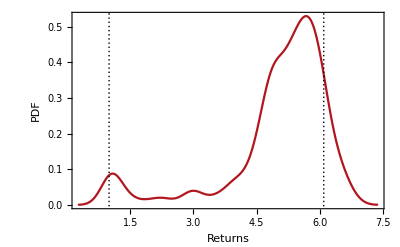

```mathematica
SmoothHistogram[population[[All,"Profit"]],
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Returns",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{1,bAndhAvgRet},{}},
PlotStyle->colors[[1]]
]
```

```mathematica
Max[population[[All,"Profit"]]]
```

6.76377

```mathematica
survivors = 100;
mutationProb = 0.4;
elitism = 5;
transactionCost = 0.0025;
```

```mathematica
nextGen = Generation[population,survivors,mutationProb,elitism,transactionCost];
```

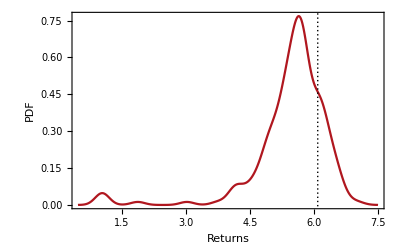

```mathematica
SmoothHistogram[nextGen[[All,"Profit"]],
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Returns",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{bAndhAvgRet},{}},
PlotStyle->colors[[1]]
]
```

```mathematica
Median[nextGen[[All,"Profit"]]]
```

5.62192

```mathematica
Max[nextGen[[All,"Profit"]]]
```

7.02098

```mathematica
nextGen2 = Generation[nextGen,survivors,mutationProb,elitism,transactionCost];
```

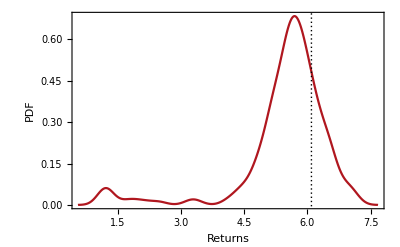

```mathematica
SmoothHistogram[nextGen2[[All,"Profit"]],
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome",
FrameLabel->{Style["Returns",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{bAndhAvgRet},{}},
PlotStyle->colors[[1]]
]
```

```mathematica
Median[nextGen2[[All,"Profit"]]]
```

5.67647

```mathematica
Max[nextGen2[[All,"Profit"]]]
```

7.12012

```mathematica
nextGen3 = Generation[nextGen2,survivors,mutationProb,elitism,transactionCost];
```

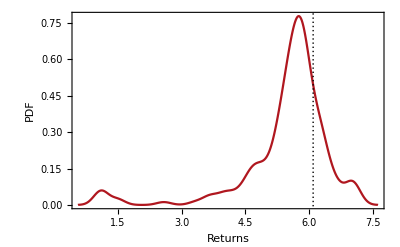

```mathematica
SmoothHistogram[nextGen3[[All,"Profit"]],
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Returns",15], Style["PDF",15]},
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{bAndhAvgRet},{}},
PlotStyle->colors[[1]]
]
```

```mathematica
Median[nextGen3[[All,"Profit"]]]
```

5.68899

```mathematica
Max[nextGen3[[All,"Profit"]]]
```

7.12012

### Non-interactive evolution

```mathematica
EvolvePopulation[population_,survivors_,mutationProb_,elitism_, profitTake_,stopLoss_,transactionCost_,generations_]:=
ProgressNestList[
Generation[#,survivors,mutationProb,elitism, profitTake,stopLoss,transactionCost]&,
population,generations,
"Label"->"Generation"
];
```

#### First round:

```mathematica
bAndhAvgRet = Mean[Map[BuyAndHoldReturn[#,0.0025]&,stockNames]]
```

6.09555

```mathematica
survivors = 100;
mutationProb = 0.4;
elitism = 5;
transactionCost = 0.0025;
```

```mathematica
population = GenerateQualifiedPopulation[200,0.0025,500];
```

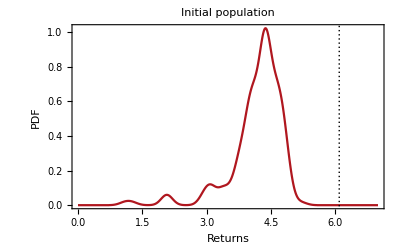

```mathematica
SmoothHistogram[population[[All,"Profit"]],
PlotRange->{{0,7},All},
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Returns",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{bAndhAvgRet},{}},
PlotStyle->colors[[1]],
PlotLabel->"Initial population"
]
```

```mathematica
evolution = EvolvePopulation[population,survivors,mutationProb,elitism,transactionCost,20];
```

```mathematica
mediansVsGen = Map[Median,evolution[[All,All,"Profit"]]]
```

{5.32388,5.67779,5.69118,5.75441,5.67368,5.67699,5.70693,5.66838,5.62916,5.70453,5.71054,5.69131,5.66068,5.67618,5.74643,5.72762,5.79202,5.72875,5.6542,5.68316,5.72931}

```mathematica
bAndhAvgRet
```

6.09555

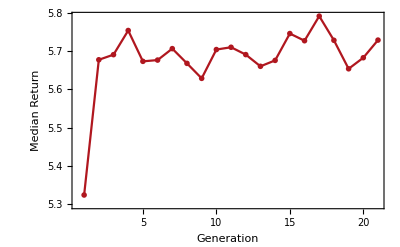

```mathematica
ListLinePlot[mediansVsGen,
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Generation",15], Style["Median Return",15]}, 
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{},{bAndhAvgRet}},
PlotStyle->colors[[1]]
]
```

```mathematica
maxVsGen = Map[Max,evolution[[All,All,"Profit"]]]
```

{6.76377,6.93498,7.06271,7.06271,7.06271,7.06271,7.06271,7.06271,7.06271,7.06271,7.06271,7.21608,7.21608,7.21608,7.21608,7.42462,7.42462,7.42462,7.42462,7.42462,7.42462}

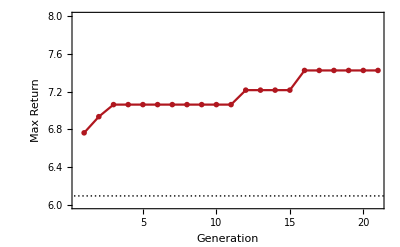

```mathematica
ListLinePlot[maxVsGen,
PlotRange->{All,{6,8}},
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Generation",15], Style["Max Return",15]}, 
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{},{bAndhAvgRet}},
PlotStyle->colors[[1]]
]
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"evolution20.wdx"}],evolution]
```

C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\evolution20.wdx

#### Second round:

```mathematica
evolution2 = EvolvePopulation[Last[evolution],survivors,mutationProb,elitism,inmigration,transactionCost,30];
```

#### Full

```mathematica
fullEvolution = Join[evolution,Drop[evolution2,1]];
```

```mathematica
mediansVsGen = Map[Median,fullEvolution[[All,All,"Profit"]]];
```

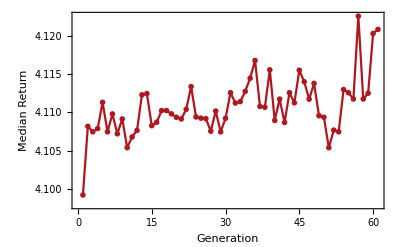

```mathematica
ListLinePlot[mediansVsGen,
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Generation",15], Style["Median Return",15]}, 
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{},{bAndhAvgRet}},
PlotStyle->colors[[1]]
]
```

```mathematica
maxVsGen = Map[Max,fullEvolution[[All,All,"Profit"]]]
```

{4.37979,4.37979,4.37979,4.37979,4.37979,4.37979,4.37979,4.37979,4.37979,4.37979,4.37979,4.37979,4.37979,4.37979,4.37979,4.37979,4.37979,4.37979,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013,4.48013}

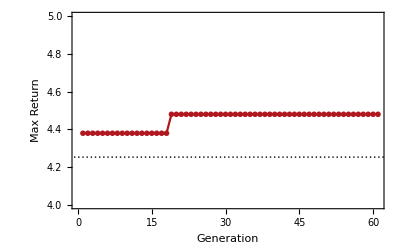

```mathematica
ListLinePlot[maxVsGen,
PlotRange->{All,{4,5}},
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Generation",15], Style["Max Return",15]}, 
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{},{bAndhAvgRet}},
PlotStyle->colors[[1]]
]
```

```mathematica
top10 = Take[Reverse[SortBy[Last[evolution],Key["Profit"]]],10];
```

```mathematica
Map[{#["ExitConditions"],SynthesizeFunction[#["Genome"]]}&,top10]
```

{{{0.795034,-0.39566},Indicator[TradingVolume,stock,time]>IndQuantile[TradingVolume,0.15,stock,time]},{{0.795034,-0.39566},IndQuantile[ClosingBias,0.75,stock,time]>Indicator[ClosingBias,stock,time]},{{0.79673,-0.395319},Indicator[TradingVolume,stock,time]>IndQuantile[TradingVolume,0.25,stock,time]},{{0.780469,-0.411271},Indicator[TradingVolume,stock,time]>IndQuantile[TradingVolume,0.15,stock,time]},{{0.480754,-0.332165},Indicator[MedianPrice,stock,time]<IndQuantile[MedianPrice,0.95,stock,time]},{{0.750497,-0.359724},IndQuantile[PricePercentangeChangeOpenToClose,0.15,stock,time]>Indicator[ExtensionRatio,stock,time]},{{0.487787,-0.746682},IndQuantile[PricePercentangeChangeOpenToClose,0.25,stock,time]≤Indicator[PricePercentangeChangeOpenToClose,stock,time]},{{0.444391,-0.627767},Indicator[TypicalPrice,stock,time]≥IndQuantile[TypicalPrice,0.05,stock,time]},{{0.754628,-0.806998},Indicator[ExtensionRatio,stock,time]>IndQuantile[PricePercentangeChangeOpenToClose,0.95,stock,time]},{{0.738146,-0.710795},IndQuantile[PricePercentangeChangeOpenToClose,0.75,stock,time]≥Indicator[ExtensionRatio,stock,time]}}

```mathematica
top10[[All,"Profit"]]
```

{4.48013,4.43733,4.43585,4.43366,4.42658,4.42308,4.42076,4.37979,4.30807,4.30595}

```mathematica
favStrategy = IndQuantile[HighPrice[#stock,#time],0.85]≥IndQuantile[ClosePrice[#stock,#time],0.95]&&IndQuantile[LowPrice[#stock,#time],0.95]≥TypicalPrice[#stock,#time]
```

IndQuantile[HighPrice[#stock,#time],0.85]≥IndQuantile[ClosePrice[#stock,#time],0.95]&&IndQuantile[LowPrice[#stock,#time],0.95]≥TypicalPrice[#stock,#time]

```mathematica
bestStrategyReturns = Map[BacktestStrategyFunction[#,favStrategy,pProfitTake,pLossExit,0.0025]&,stockNames]
```

{{1.51968,1.50848,1.50221,1.49749,1.6069,1.21448},{1.51271,1.50529,1.50307,1.45163},{1.4948,1.50043,1.51475,0.997928},{1.49344,1.49354,1.511,1.50302,0.427835,1.6164,1.64155,1.22941},{1.49337,1.50326,1.04552},{1.53274,1.49375,1.49468,1.53082,1.53956,0.865666},{1.49738,1.49858,1.03115},{1.0526},{1.49289,1.4959,1.49756,1.27902},{1.49519,1.33237},{1.51471,1.5475,1.4942,1.5107,1.49843},{1.49449,1.49256,1.49318,1.26566},{0.860187},{1.58443,1.49924,1.22407},{1.51361,1.51807,1.15415},{1.49531,1.50522,1.50956,0.97959},{1.5013,1.16081},{1.50152,1.49589,1.36779},{1.49847,1.49386,1.05017},{1.4957,1.50303,1.09084},{1.49376,1.50757,1.49424,1.50041,1.49467,1.25214},{1.49803,1.49649,1.50408,1.49448,1.21443},{1.49284,1.49359,0.985435},{1.49503,1.50303,1.20979},{1.49808,1.50944,1.49309,1.53271,1.49792,1.22261},{1.49266,1.49346,1.51179,1.49844,1.49946,1.49394,1.49648,1.10581},{1.4969,1.05067},{1.52203,0.803292},{1.5093,1.503,1.0931}}

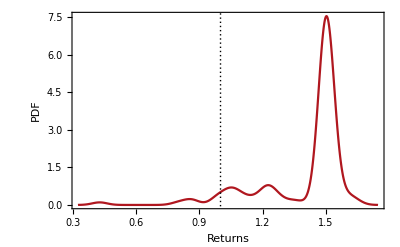

```mathematica
SmoothHistogram[
Flatten[bestStrategyReturns],
PlotRange->All,
Frame->True,
PlotTheme->"Monochrome", 
FrameLabel->{Style["Returns",15], Style["PDF",15]}, 
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{1},{}},
PlotStyle->colors[[1]]
]
```

### Interactive evolution

#### Implementation:

```mathematica
GetSeconds[time_] := IntegerString[Round[Mod[time, 60]], 10, 2];
GetMinutes[time_]:= IntegerString[Mod[Floor[time/60], 60], 10, 2];
GetHours[time_] := IntegerString[Floor[time/3600], 10, 2];
ClockFormat[time_] := StringJoin[GetHours[time], ":", GetMinutes[time], ":", GetSeconds[time]];

ProgressEvolveIndicator[indexProgress_,totalSize_,startTime_,fittestIndPlot_,averageIndPlot_,worstIndPlot_,meanScorePlot_,maxScorePlot_,scoresHistogram_,popSize_]:=Block[{progressString,remainingTime,remainingTimeString,indicator,ellapsedTimeString},
progressString = Row[{Style["Progress: ",Bold],ToString[indexProgress],"/",ToString[totalSize]}];
ellapsedTimeString = Row[{Style["Ellapsed time: ",Bold],ClockFormat[AbsoluteTime[]-startTime]}];

If[indexProgress ≠ 0,
remainingTime = (AbsoluteTime[]-startTime)/indexProgress(totalSize-indexProgress);
remainingTimeString = Row[{Style["Remaining: ",Bold],ClockFormat[remainingTime]}];
,
remainingTimeString = Row[{Style["Remaining: ", Bold],"Unknown"}];
];

indicator = Panel[
Column[
{
Style["Generation",Bold],
ProgressIndicator[indexProgress,{1,totalSize}],
progressString,
ellapsedTimeString,
remainingTimeString,
Row[{Style["Population size: ", Bold],popSize}],
Style["Scores: ", Bold],
Row[{meanScorePlot,maxScorePlot,scoresHistogram}],
Style["Fittest individuals: ", Bold],
fittestIndPlot,
Style["Average individuals: ", Bold],
averageIndPlot,
Style["Worst individuals: ", Bold],
worstIndPlot
}
]
];

Return[indicator];
];
ProgressEvolvePopulation[population_,survivors_,mutationProb_,elitism_, profitTake_,stopLoss_,transactionCost_,generations_]:=Block[{meanScorePlot,fittestIndPlot,currentGeneration = population,startTime = AbsoluteTime[],indexProgress = 0,meanScoreVsK={},meanValidationVsK={},accuracyVsK={},allGenerations={population},scoresHistogram,averagePos,averageIndPlot,worstIndPlot,bAndhAvgRetTraining,bAndhAvgRetValidation,validationScore,best,validationBest,trainingVsValidationByGen,accuracyVsKPlot,localPath},

localPath = NotebookDirectory[];
BTSwitchToDataset["TrainingSet"];
bAndhAvgRetTraining = Mean[Map[BuyAndHoldReturn[#,transactionCost]&,stockNames]];

BTSwitchToDataset["ValidationSet"];
bAndhAvgRetValidation = Mean[Map[BuyAndHoldReturn[#,transactionCost]&,stockNames]];
BTSwitchToDataset["TrainingSet"];

Monitor[
Do[
validationScore = EvaluatePopulation[currentGeneration,profitTake,stopLoss,transactionCost,"ValidationSet"];

AppendTo[meanScoreVsK,Mean[currentGeneration[[All,"Profit"]]]];
AppendTo[meanValidationVsK,Mean[validationScore[[All,"Profit"]]]];

meanScorePlot = ListLinePlot[
{meanScoreVsK,meanValidationVsK},
PlotTheme->"Monochrome",
FrameLabel->{Style["Generation",15], Style["Average Profit",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{},{0,bAndhAvgRetTraining,bAndhAvgRetValidation}},
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0., 0.61, 0.3]},
PlotLabel->"Avg Profit",
Frame->True,
ImageSize->400,
PlotRange->All,
PlotLegends->{"TrainingSet","ValidationSet"}
];


trainingVsValidationByGen = Transpose[{currentGeneration[[All,"Profit"]],validationScore[[All,"Profit"]]}];
AppendTo[accuracyVsK , Count[trainingVsValidationByGen,{x_,y_}/;(x>bAndhAvgRetTraining)&&(y>bAndhAvgRetValidation)]/Length[trainingVsValidationByGen]];

accuracyVsKPlot = ListLinePlot[
accuracyVsK,
PlotTheme->"Monochrome",
FrameLabel->{Style["Generation",15], Style["Accuracy",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
PlotStyle->{RGBColor[0., 0.61, 0.3]},
PlotLabel->"Accuracy",
Frame->True,
ImageSize->400,
PlotRange->All
];

fittestIndPlot = Grid[Map[{SynthesizeTree[#["Genome"]],#["Profit"]}&,Take[currentGeneration,3]],Frame->All];
averagePos = Floor[Length[currentGeneration]/2];
averageIndPlot = Grid[Map[{SynthesizeTree[#["Genome"]],#["Profit"]}&,Take[currentGeneration,{averagePos-1,averagePos+1}]],Frame->All];
worstIndPlot = Grid[Map[{SynthesizeTree[#["Genome"]],#["Profit"]}&,Take[currentGeneration,-3]],Frame->All];

scoresHistogram = ListPlot[trainingVsValidationByGen,
AspectRatio->1,
PlotTheme->"Monochrome",
PlotStyle->{colors[[1]]},
Frame->True,
FrameLabel->{Style["Training score",15],Style["Validation score",15]},
BaseStyle->FontSize->14,
GridLines->{{bAndhAvgRetTraining},{bAndhAvgRetValidation}},
PlotRange->{{0.9,1.1},{0.9,1.1}},
ImageSize->400
];

currentGeneration = Generation[currentGeneration,survivors,mutationProb,elitism, profitTake,stopLoss,transactionCost];
AppendTo[allGenerations,currentGeneration];
indexProgress++;
,generations
],
ProgressEvolveIndicator[indexProgress,generations,startTime,fittestIndPlot,averageIndPlot,worstIndPlot,meanScorePlot,accuracyVsKPlot,scoresHistogram,Length[currentGeneration]]
];

Return[allGenerations];
];
```

#### Example:

```mathematica
survivors = 100;
mutationProb = 0.4;
elitism = 20;
transactionCost = 0.0005;
profitTake = 0.03;
stopLoss = -0.03;
```

```mathematica
population = GenerateQualifiedPopulation[200,profitTake,stopLoss,0.0005,500];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"initialPopulation_ProfitTakeStopLoss_01-01.wdx"}],population]
```

/home/carlos/Documentos/Programacion/GrammarBasedTradingStrategyV2/initialPopulation_ProfitTakeStopLoss_02-03.wdx

```mathematica
population = Import[FileNameJoin[{NotebookDirectory[],"initialPopulation_ProfitTakeStopLoss3.wdx"}]];
```

```mathematica
generations = ProgressEvolvePopulation[population,survivors,mutationProb,elitism,profitTake,stopLoss,transactionCost,130];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"evolution_ProfitTakeStopLoss_UtilitiesRegulatedElectric_0.03-0.03.wdx"}],generations]
```

/home/carlos/Documentos/Programacion/GrammarBasedTradingStrategyV2/IntradayExperiments/evolution_ProfitTakeStopLoss_UtilitiesRegulatedElectric_0.03-0.03.wdx

```mathematica
generations = Import[FileNameJoin[{NotebookDirectory[],"evolution_ProfitTakeStopLoss_UtilitiesRegulatedElectric_0.03-0.03.wdx"}]];
```

```mathematica
validationScores = ProgressTable[EvaluatePopulation[generations[[i]],profitTake,stopLoss,transactionCost,"ValidationSet"],{i,1,Length[generations]}];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"validation_ProfitTakeStopLoss_UtilitiesRegulatedElectric_0.03-0.03.wdx"}],validationScores]
```

/home/carlos/Documentos/Programacion/GrammarBasedTradingStrategyV2/IntradayExperiments/validation_ProfitTakeStopLoss_UtilitiesRegulatedElectric_0.03-0.03.wdx

```mathematica
validationScores = Import[FileNameJoin[{NotebookDirectory[],"validation_ProfitTakeStopLoss_UtilitiesRegulatedElectric_0.03-0.03.wdx"}]];
```

### Get run results

Do strategies generalize over different sets?

```mathematica
trainingVsValidationByGen = MapThread[Transpose[{#1[[All,"Profit"]],#2[[All,"Profit"]]}]&,{generations,validationScores}];
```

```mathematica
corrCoefficients = Map[Apply[Correlation,Transpose[#]]&,trainingVsValidationByGen];
```

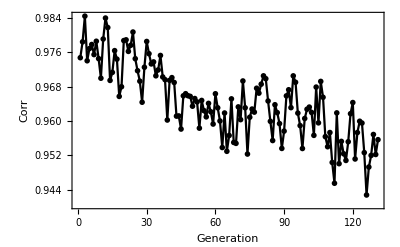

```mathematica
ListLinePlot[corrCoefficients,
PlotRange->All,
PlotTheme->"Monochrome",
PlotStyle->{colors[[2]]},
Frame->True,
FrameLabel->{Style["Generation",15],Style["Corr",15]},
BaseStyle->FontSize->14
]
```

```mathematica
Manipulate[
ListPlot[trainingVsValidationByGen[[i]],
AspectRatio->1,
PlotTheme->"Monochrome",
PlotStyle->{colors[[1]]},
Frame->True,
FrameLabel->{Style["Training score",15],Style["Validation score",15]},
BaseStyle->FontSize->14,
GridLines->{{bAndhAvgRetTraining},{bAndhAvgRetValidation}},
PlotRange->{{0.9,1.1},{0.9,1.2}}
],
{i,1,Length[trainingVsValidationByGen],1},
SaveDefinitions->True
]
```

Does population gene pool improve over time?

```mathematica
accuracyByGen = Table[{i,Count[trainingVsValidationByGen[[i]],{x_,y_}/;(x>bAndhAvgRetTraining)&&(y>bAndhAvgRetValidation)]/Length[trainingVsValidationByGen[[i]]]},{i,1,Length[trainingVsValidationByGen]}];
```

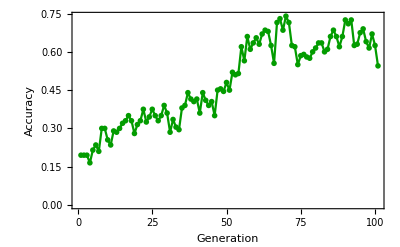

```mathematica
ListLinePlot[
accuracyByGen,
PlotRange->All,
PlotTheme->"Monochrome",
PlotStyle->{colors[[4]]},
Frame->True,
FrameLabel->{Style["Generation",15],Style["Accuracy",15]},
BaseStyle->FontSize->14
]
```

```mathematica
meanValidation = Map[Mean,validationScores[[All,All,"Profit"]]];
```

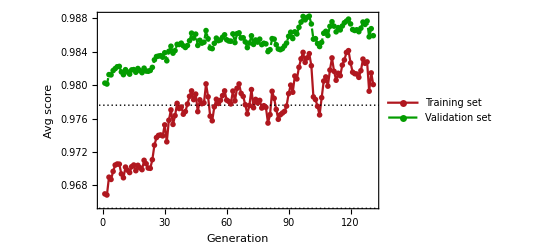

```mathematica
ListLinePlot[
{Map[Mean,generations[[All,All,"Profit"]]],Map[Mean,validationScores[[All,All,"Profit"]]]},
PlotRange->All,
PlotTheme->"Monochrome",
PlotStyle->{colors[[1]],colors[[4]]},
Frame->True,
FrameLabel->{Style["Generation",15],Style["Avg score",15]},
BaseStyle->FontSize->14,
PlotLegends->{"Training set", "Validation set"},
GridLines->{{},{bAndhAvgRetTraining, bAndhAvgRetValidation}}
]
```

```mathematica
bestOfTraining = Map[First[MaximalBy[#,Key["Profit"]]]&,generations];
```

```mathematica
bestOfValidation = EvaluatePopulation[bestOfTraining,profitTake,stopLoss,transactionCost,"ValidationSet"];
```

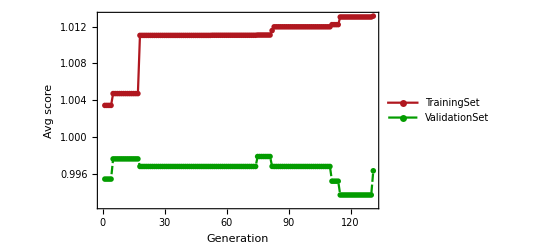

```mathematica
ListLinePlot[
{Map[Max,generations[[All,All,"Profit"]]],bestOfValidation[[All,"Profit"]]},
PlotRange->All,
PlotTheme->"Monochrome",
PlotStyle->{colors[[1]],colors[[4]]},
Frame->True,
FrameLabel->{Style["Generation",15],Style["Avg score",15]},
BaseStyle->FontSize->14,
PlotLegends->{"TrainingSet","ValidationSet"},
GridLines->{{},{bAndhAvgRetTraining, bAndhAvgRetValidation}}
]
```

### Study of best strategies

```mathematica
testingScores = Last[generations];
```

```mathematica
top10 = Take[Reverse[SortBy[testingScores,Key["Profit"]]],10];
```

```mathematica
worse10 = Take[Reverse[SortBy[testingScores,Key["Profit"]]],-10];
```

```mathematica
top10Synth = Map[SynthesizeFunction[#["Genome"]]&,top10]
```

{IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&((IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[EMA,0.85,stock,time]≥Indicator[MedianPrice,stock,time])||IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.95,stock,time])&&IndQuantile[MedianPrice,0.15,stock,time]≤Indicator[WeightedClose,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&IndQuantile[ClosePrice,0.15,stock,time]≤IndQuantile[VWAP,0.95,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[OpenPrice,0.75,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[EMA,0.95,stock,time]≤IndQuantile[VWAP,0.95,stock,time]&&IndQuantile[ClosePrice,0.15,stock,time]≤IndQuantile[OpenPrice,0.25,stock,time]&&IndQuantile[EMA,0.85,stock,time]≤IndQuantile[VWAP,0.75,stock,time],IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&((IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[EMA,0.85,stock,time]≥Indicator[MedianPrice,stock,time])||IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.95,stock,time])&&IndQuantile[MedianPrice,0.15,stock,time]≤Indicator[WeightedClose,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&IndQuantile[ClosePrice,0.15,stock,time]≤IndQuantile[VWAP,0.95,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[OpenPrice,0.75,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[ClosePrice,0.15,stock,time]≤IndQuantile[OpenPrice,0.25,stock,time]&&IndQuantile[EMA,0.85,stock,time]≤IndQuantile[VWAP,0.75,stock,time],IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&((IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[EMA,0.85,stock,time]≥Indicator[MedianPrice,stock,time])||IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.95,stock,time])&&IndQuantile[MedianPrice,0.15,stock,time]≤Indicator[WeightedClose,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&IndQuantile[ClosePrice,0.15,stock,time]≤IndQuantile[VWAP,0.95,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[OpenPrice,0.75,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[ClosePrice,0.15,stock,time]≤IndQuantile[OpenPrice,0.25,stock,time]&&IndQuantile[MedianPrice,0.15,stock,time]≤Indicator[WeightedClose,stock,time],(IndQuantile[EMA,0.85,stock,time]>IndQuantile[VWAP,0.95,stock,time]||(IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&IndQuantile[HighPrice,0.25,stock,time]≥Indicator[OpenPrice,stock,time])||IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.95,stock,time])&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[OpenPrice,0.75,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[LowPrice,0.05,stock,time]≤IndQuantile[VWAP,0.95,stock,time],(IndQuantile[EMA,0.85,stock,time]>IndQuantile[VWAP,0.95,stock,time]||(IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&IndQuantile[EMA,0.25,stock,time]≥Indicator[OpenPrice,stock,time])||IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.95,stock,time])&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[OpenPrice,0.75,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[LowPrice,0.05,stock,time]≤IndQuantile[VWAP,0.95,stock,time],IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&((IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[EMA,0.25,stock,time]≥Indicator[MedianPrice,stock,time])||IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.95,stock,time])&&IndQuantile[MedianPrice,0.15,stock,time]≤Indicator[WeightedClose,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&IndQuantile[ClosePrice,0.15,stock,time]≤IndQuantile[OpenPrice,0.25,stock,time],IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&((IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[EMA,0.85,stock,time]≥Indicator[MedianPrice,stock,time])||IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.95,stock,time])&&IndQuantile[MedianPrice,0.15,stock,time]≤Indicator[WeightedClose,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&IndQuantile[ClosePrice,0.15,stock,time]≤IndQuantile[VWAP,0.95,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[OpenPrice,0.75,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[EMA,0.95,stock,time]≤IndQuantile[VWAP,0.95,stock,time]&&IndQuantile[EMA,0.85,stock,time]≤IndQuantile[VWAP,0.75,stock,time],(IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.95,stock,time]||(IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&IndQuantile[EMA,0.25,stock,time]≥Indicator[OpenPrice,stock,time])||IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.95,stock,time])&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[OpenPrice,0.75,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[LowPrice,0.05,stock,time]≤IndQuantile[VWAP,0.95,stock,time],IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&((IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[EMA,0.85,stock,time]≥Indicator[MedianPrice,stock,time])||IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.95,stock,time])&&IndQuantile[MedianPrice,0.15,stock,time]≤Indicator[WeightedClose,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&IndQuantile[ClosePrice,0.15,stock,time]≤IndQuantile[VWAP,0.95,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[OpenPrice,0.75,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[LowPrice,0.05,stock,time]≤IndQuantile[VWAP,0.95,stock,time],(IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.95,stock,time]||(IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥Indicator[MedianPrice,stock,time])||IndQuantile[SMA,0.25,stock,time]>IndQuantile[SMA,0.85,stock,time])&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[OpenPrice,0.75,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[OpenPrice,0.75,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[LowPrice,0.05,stock,time]≤IndQuantile[VWAP,0.95,stock,time]}

```mathematica
worse10Synth = Map[SynthesizeFunction[#["Genome"]]&,worse10]
```

{IndQuantile[ClosingBias,0.75,stock,time]≥25,IndQuantile[ExtensionRatio,0.95,stock,time]>0,IndQuantile[OpenPrice,0.05,stock,time]≤Indicator[EMA,stock,time],Indicator[ROC,stock,time]<IndQuantile[ExtensionRatio,0.75,stock,time],75≥IndQuantile[RSI,0.05,stock,time],IndQuantile[OBV,0.85,stock,time]<Indicator[OBV,stock,time]||(Indicator[ClosingBias,stock,time]>Indicator[RSI,stock,time]&&Indicator[RSI,stock,time]≤IndQuantile[MFI,0.85,stock,time]),IndQuantile[OBV,0.25,stock,time]≥Indicator[OBV,stock,time]||Indicator[MedianPrice,stock,time]≥IndQuantile[HighPrice,0.25,stock,time],Indicator[ClosePrice,stock,time]>Indicator[TypicalPrice,stock,time],Indicator[ExtensionRatio,stock,time]>IndQuantile[ExtensionRatio,0.75,stock,time],IndQuantile[PricePercentangeChangeOpenToClose,0.95,stock,time]<Indicator[ExtensionRatio,stock,time]||IndQuantile[TradingVolume,0.85,stock,time]<Indicator[TradingVolume,stock,time]}

```mathematica
bestStrategy = ConvertStrategyFunctionToCpp[IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&((IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[EMA,0.85,stock,time]≥Indicator[MedianPrice,stock,time])||IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.95,stock,time])&&IndQuantile[MedianPrice,0.15,stock,time]≤Indicator[WeightedClose,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&IndQuantile[ClosePrice,0.15,stock,time]≤IndQuantile[VWAP,0.95,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[OpenPrice,0.75,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[EMA,0.95,stock,time]≤IndQuantile[VWAP,0.95,stock,time]&&IndQuantile[ClosePrice,0.15,stock,time]≤IndQuantile[OpenPrice,0.25,stock,time]&&IndQuantile[EMA,0.85,stock,time]≤IndQuantile[VWAP,0.75,stock,time]];
```

```mathematica
averageStrategy = ConvertStrategyFunctionToCpp[(IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.95,stock,time]||(IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[SMA,0.85,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥Indicator[MedianPrice,stock,time])||IndQuantile[SMA,0.25,stock,time]>IndQuantile[SMA,0.85,stock,time])&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[OpenPrice,0.75,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[TypicalPrice,0.85,stock,time]>IndQuantile[OpenPrice,0.75,stock,time]&&IndQuantile[SMA,0.25,stock,time]≥IndQuantile[EMA,0.85,stock,time]&&IndQuantile[LowPrice,0.05,stock,time]≤IndQuantile[VWAP,0.95,stock,time]];
```

```mathematica
badStrategy = ConvertStrategyFunctionToCpp[IndQuantile[ClosingBias,0.75,stock,time]≥25];
```

```mathematica
BTSwitchToDataset["TrainingSet"];
```

```mathematica
bestReturns = BTGetStrategyReturnsAllStocksStoplossProfitTake["DivReturns",bestStrategy,profitTake, stopLoss,0.0005];
```

```mathematica
averageReturns = BTGetStrategyReturnsAllStocksStoplossProfitTake["DivReturns",averageStrategy,profitTake, stopLoss,0.0005];
```

```mathematica
badReturns = BTGetStrategyReturnsAllStocksStoplossProfitTake["DivReturns",badStrategy,profitTake, stopLoss,0.0005];
```

```mathematica
CondenseDivReturns[bestReturns]
```

1.01327

```mathematica
CondenseDivReturns[averageReturns]
```

1.01268

```mathematica
CondenseDivReturns[badReturns]
```

0.949694

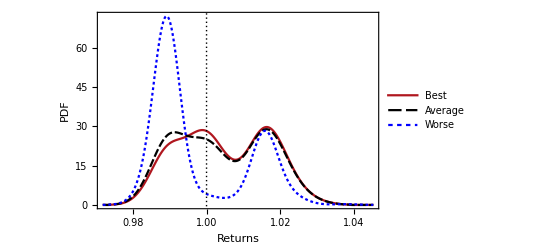

```mathematica
SmoothHistogram[
{Flatten[Values[bestReturns]],Flatten[Values[averageReturns]],Flatten[Values[badReturns]]},
PlotTheme->"Monochrome",
PlotRange->All,
Frame->True,
FrameLabel->{Style["Returns",15], Style["PDF",15]},
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{1},{}},
PlotStyle->{colors[[1]],colors[[2]],colors[[3]]},
PlotLegends->{"Best","Average","Worse"}
]
```

{0.993002,0.992669,0.974391}

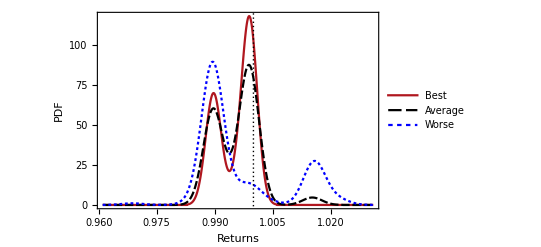

```mathematica
BTSwitchToDataset["ValidationSet"];
bestReturns = BTGetStrategyReturnsAllStocksStoplossProfitTake["DivReturns",bestStrategy,profitTake, stopLoss,0.0005];
averageReturns = BTGetStrategyReturnsAllStocksStoplossProfitTake["DivReturns",averageStrategy,profitTake, stopLoss,0.0005];
badReturns = BTGetStrategyReturnsAllStocksStoplossProfitTake["DivReturns",badStrategy,profitTake, stopLoss,0.0005];

{CondenseDivReturns[bestReturns],CondenseDivReturns[averageReturns],CondenseDivReturns[badReturns]}

SmoothHistogram[
{Flatten[Values[bestReturns]],Flatten[Values[averageReturns]],Flatten[Values[badReturns]]},
PlotTheme->"Monochrome",
PlotRange->All,
Frame->True,
FrameLabel->{Style["Returns",15], Style["PDF",15]},
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{1},{}},
PlotStyle->{colors[[1]],colors[[2]],colors[[3]]},
PlotLegends->{"Best","Average","Worse"}
]
```

```mathematica
bAndhAvgRetValidation
```

0.977609

```mathematica
CondenseDivReturns[bestReturns]/bAndhAvgRetValidation
```

1.01575

```mathematica
MarketParticipation[strategyFunc_,stock_]:=Block[{strategyValues},
strategyValues = BTGetStrategyValues[strategyFunc,stock];
N@(Count[strategyValues,True]/Count[strategyValues,False])
];
```

### Results of all runs

```mathematica
runsFiles = FileNames["*.wdx",FileNameJoin[{NotebookDirectory[],"Runs"}]]
```

{C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\Runs\evolution_ProfitTakeStopLoss02-02.wdx,C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\Runs\evolution_ProfitTakeStopLoss02-03.wdx,C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\Runs\evolution_ProfitTakeStopLoss02-04.wdx,C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\Runs\evolution_ProfitTakeStopLoss03-02.wdx,C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\Runs\evolution_ProfitTakeStopLoss03-03.wdx,C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\Runs\evolution_ProfitTakeStopLoss04-02.wdx,C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\Runs\evolution_ProfitTakeStopLoss04-04.wdx}

```mathematica
generationsVsParameters = Map[Import,runsFiles];
```

```mathematica
GetParametersFromFilename[path_]:=Map[
ToExpression,
{StringInsert[StringTake[FileBaseName[path],{-5,-4}],".",2],StringInsert[StringTake[FileBaseName[path],{-3,-1}],".",3]}
];
GetTrainingVsValidationScoreByGen[runsFile_]:=Block[{profitTake, stopLoss,generations,validationScores,trainingVsValidationByGen,fileLabel},
{profitTake, stopLoss} = GetParametersFromFilename[runsFile];
generations = Import[runsFile];
validationScores = ProgressTable[EvaluatePopulation[generations[[i]],profitTake,stopLoss,transactionCost,"ValidationSet"],{i,1,Length[generations]}];
trainingVsValidationByGen = MapThread[Transpose[{#1[[All,"Profit"]],#2[[All,"Profit"]]}]&,{generations,validationScores}];
fileLabel = StringTake[FileBaseName[runsFile],{-5,-1}];
Export[FileNameJoin[{NotebookDirectory[],"TrainingVsValidation","trVsVal_"<>fileLabel<>".wdx"}],trainingVsValidationByGen]
];
```

```mathematica
ProgressMap[GetTrainingVsValidationScoreByGen,runsFiles]
```

{/home/carlos/Documentos/Programacion/GrammarBasedTradingStrategyV2/TrainingVsValidation/trVsVal_02-02.wdx,/home/carlos/Documentos/Programacion/GrammarBasedTradingStrategyV2/TrainingVsValidation/trVsVal_02-03.wdx,/home/carlos/Documentos/Programacion/GrammarBasedTradingStrategyV2/TrainingVsValidation/trVsVal_02-04.wdx,/home/carlos/Documentos/Programacion/GrammarBasedTradingStrategyV2/TrainingVsValidation/trVsVal_03-02.wdx,/home/carlos/Documentos/Programacion/GrammarBasedTradingStrategyV2/TrainingVsValidation/trVsVal_03-03.wdx,/home/carlos/Documentos/Programacion/GrammarBasedTradingStrategyV2/TrainingVsValidation/trVsVal_04-02.wdx,/home/carlos/Documentos/Programacion/GrammarBasedTradingStrategyV2/TrainingVsValidation/trVsVal_04-04.wdx}

```mathematica
trainingVsValidationFiles = FileNames["*.wdx",FileNameJoin[{NotebookDirectory[],"TrainingVsValidation"}]]
```

{C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\TrainingVsValidation\trVsVal_02-02.wdx,C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\TrainingVsValidation\trVsVal_02-03.wdx,C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\TrainingVsValidation\trVsVal_02-04.wdx,C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\TrainingVsValidation\trVsVal_03-02.wdx,C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\TrainingVsValidation\trVsVal_03-03.wdx,C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\TrainingVsValidation\trVsVal_04-02.wdx,C:\Users\hp\Documents\Programacion\GrammarBasedTradingStrategyV2\TrainingVsValidation\trVsVal_04-04.wdx}

```mathematica
trainingVsValidationScores = Map[<|"Parameters"->GetParametersFromFilename[#],"Scores"->Import[#]|>&,trainingVsValidationFiles];
```

Scores plots

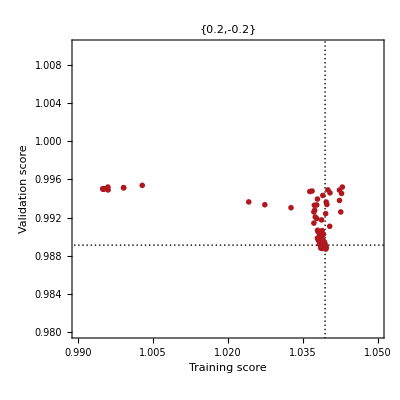
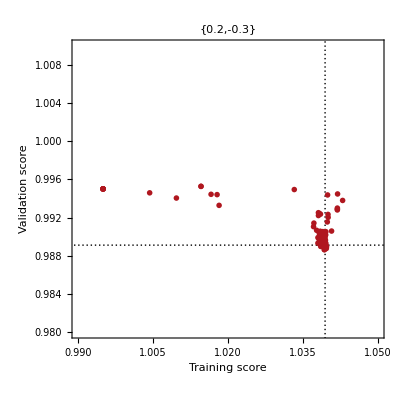
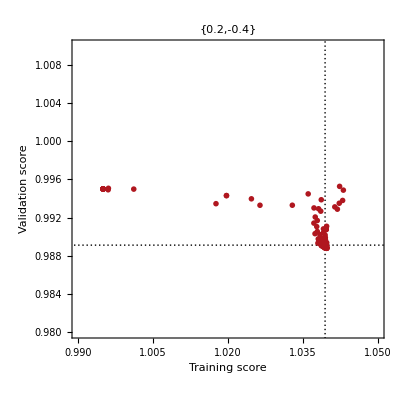
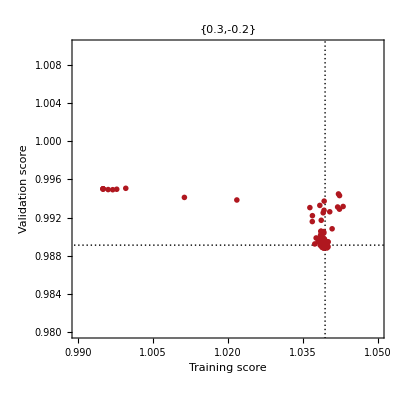
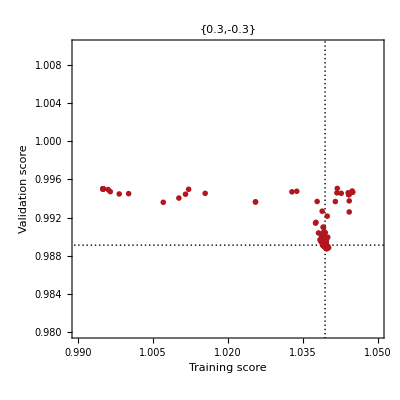
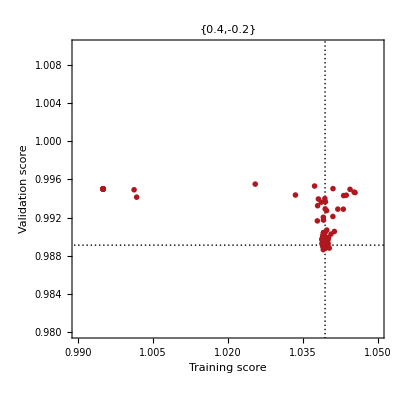
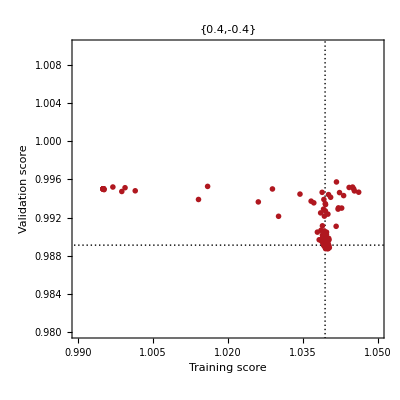

```mathematica
Map[
ListPlot[Last[#["Scores"]],
AspectRatio->1,
PlotTheme->"Monochrome",
PlotStyle->{colors[[1]]},
Frame->True,
FrameLabel->{Style["Training score",15],Style["Validation score",15]},
BaseStyle->FontSize->14,
GridLines->{{bAndhAvgRetTraining},{bAndhAvgRetValidation}},
PlotRange->{{0.99,1.05},{0.98,1.01}},
PlotLabel->#["Parameters"],
ImageSize->400
]&,
trainingVsValidationScores
]
```

Accuracy plots

```mathematica
CalculateAccuracyByGen[scores_]:=Table[{i,N[Count[scores[[i]],{x_,y_}/;(x>bAndhAvgRetTraining)&&(y>bAndhAvgRetValidation)]/Length[scores[[i]]]]},{i,1,Length[scores]}];
```

```mathematica
accuracies = Map[CalculateAccuracyByGen[#["Scores"]]&,trainingVsValidationScores];
```

```mathematica
parametersAsStrings = Map[ToString,trainingVsValidationScores[[All,"Parameters"]]];
```

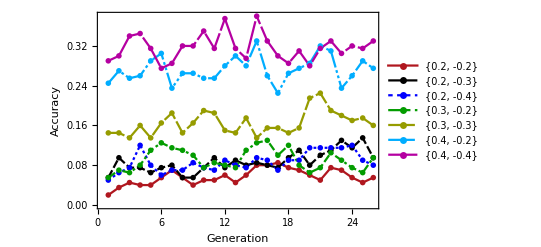

```mathematica
ListLinePlot[accuracies,
PlotLegends->parametersAsStrings,
PlotRange->All,
PlotTheme->"Monochrome",
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.01, 0.61, 0.],RGBColor[0.59, 0.61, 0.],RGBColor[0, 0.68, 1],RGBColor[0.71, 0., 0.63]},
Frame->True,
FrameLabel->{Style["Generation",15],Style["Accuracy",15]},
BaseStyle->FontSize->14,
ImageSize->400
]
```

Maximum return on training set

```mathematica
maxTrainingScores = Table[Map[First[MaximalBy[#,First]][[1]]&,trainingVsValidationScores[[i,"Scores"]]],{i,1,Length[trainingVsValidationScores]}];
```

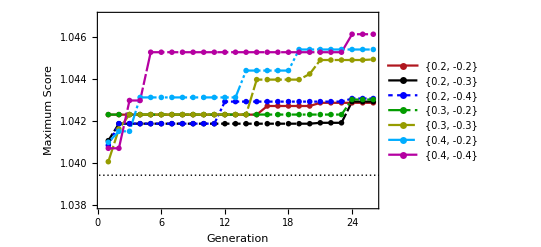

```mathematica
ListLinePlot[maxTrainingScores,
PlotLegends->parametersAsStrings,
PlotRange->{All,{1.038,1.047}},
PlotTheme->"Monochrome",
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.01, 0.61, 0.],RGBColor[0.59, 0.61, 0.],RGBColor[0, 0.68, 1],RGBColor[0.71, 0., 0.63]},
Frame->True,
FrameLabel->{Style["Generation",15],Style["Maximum Score",15]},
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{},{bAndhAvgRetTraining}}
]
```

Maximum return strategy evaluated on validation set

```mathematica
maxValidationScores = Table[Map[First[MaximalBy[#,First]][[2]]&,trainingVsValidationScores[[i,"Scores"]]],{i,1,Length[trainingVsValidationScores]}];
```

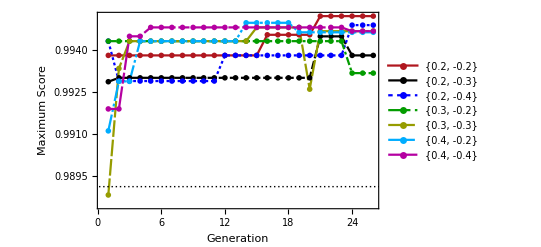

```mathematica
ListLinePlot[maxValidationScores,
PlotLegends->parametersAsStrings,
PlotRange->All,
PlotTheme->"Monochrome",
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.01, 0.61, 0.],RGBColor[0.59, 0.61, 0.],RGBColor[0, 0.68, 1],RGBColor[0.71, 0., 0.63]},
Frame->True,
FrameLabel->{Style["Generation",15],Style["Maximum Score",15]},
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{},{bAndhAvgRetValidation}}
]
```

Accurate strategies evaluated on the testing set

```mathematica
GetAccurateStrategiesIndex[scores_]:=Table[{i,Position[scores[[i]],{x_,y_}/;(x>bAndhAvgRetTraining)&&(y>bAndhAvgRetValidation)]},{i,1,Length[scores]}];
CalculateAvgReturnForAccurate[generations_,trainingVsValidationScores_]:=Block[{accurateIndexes,accurateByGeneration,profitTake,stopLoss},
accurateIndexes = GetAccurateStrategiesIndex[trainingVsValidationScores["Scores"]];
{profitTake,stopLoss}=trainingVsValidationScores["Parameters"];
accurateByGeneration = MapThread[Extract[generations[[#1]],#2]&,Transpose[accurateIndexes]];

ProgressTable[Mean[EvaluatePopulation[accurateByGeneration[[i]],profitTake,stopLoss,transactionCost,"TestingSet"][[All,"Profit"]]],{i,1,Length[accurateByGeneration]}]
];
```

```mathematica
testingAvgReturns = MapThread[CalculateAvgReturnForAccurate,{generationsVsParameters,trainingVsValidationScores}];
```

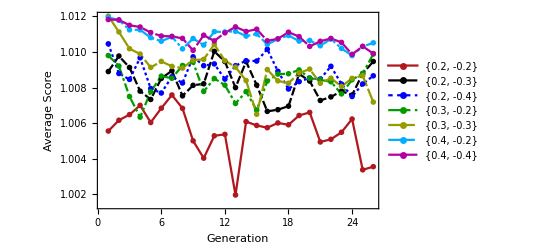

```mathematica
ListLinePlot[testingAvgReturns,
PlotLegends->parametersAsStrings,
PlotRange->All,
PlotTheme->"Monochrome",
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],GrayLevel[0],RGBColor[0, 0, 1],RGBColor[0.01, 0.61, 0.],RGBColor[0.59, 0.61, 0.],RGBColor[0, 0.68, 1],RGBColor[0.71, 0., 0.63]},
Frame->True,
FrameLabel->{Style["Generation",15],Style["Average Score",15]},
BaseStyle->FontSize->14,
ImageSize->400,
GridLines->{{},{bAndhAvgRetTesting}}
]
```

## Visualization of patterns

```mathematica
OHLCVTimeSeriesPlot[stock_,time_,window_]:=Block[{size,startIndex,endIndex,pricesOHLCV},
size = BTGetNumberOfDates[stock];
startIndex = Ramp[time-window-1]+1;
endIndex = Clip[time+2window,{startIndex,size}];

pricesOHLCV = Table[{BTGetDate[stock,i],{BTGetIndicator["OpenPrice",stock,i],BTGetIndicator["HighPrice",stock,i],BTGetIndicator["LowPrice",stock,i],BTGetIndicator["ClosePrice",stock,i],BTGetIndicator["TradingVolume",stock,i]}},{i,startIndex,endIndex}];

TradingChart[pricesOHLCV,
GridLines->{{20},{}},
PerformanceGoal->"Speed",
PlotLabel->BTGetDate[stock,time],
ImageSize->400
]
];
```

```mathematica
bestStrategy
```

IndQuantile("ClosingBias","0.05",stock,time)>=Indicator("ClosingBias",stock,time)&&(IndQuantile("ExtensionRatio","0.75",stock,time)>Indicator("PricePercentangeChangeOpenToClose",stock,time)||(IndQuantile("PricePercentangeChangeOpenToClose","0.25",stock,time)>=Indicator("ExtensionRatio",stock,time)&&IndQuantile("RSI","0.85",stock,time)<IndQuantile("RSI","0.95",stock,time))||IndQuantile("OpenPrice","0.15",stock,time)>Indicator("SMA",stock,time))

```mathematica
executionData = BTGetStrategyExecutionDataStoplossProfitTake[bestStrategy,"AAPL",profitTake,stopLoss,transactionCost];
buyTimeIndexes = Cases[executionData,KeyValuePattern["Signal"->"Buy"]][[All,"TimeIndex"]];
```

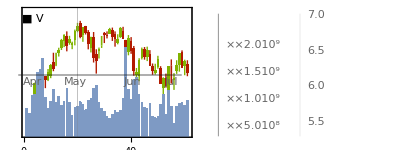
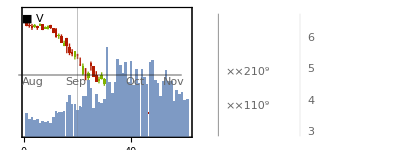
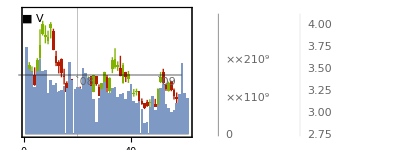
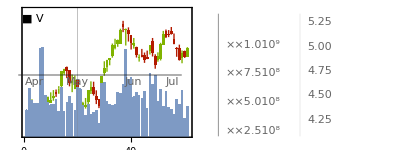
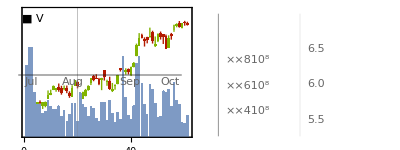
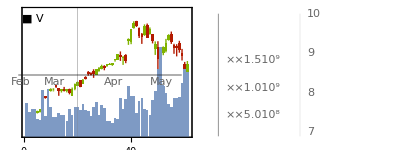
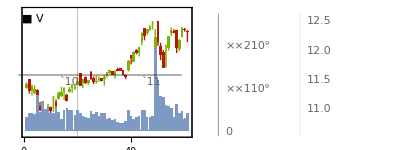
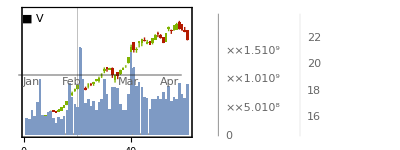

```mathematica
ProgressMap[OHLCVTimeSeriesPlot["AAPL",#,20]&,buyTimeIndexes]
```

## Eye candy

```mathematica
ViewEvolution[generations_,i_,transactionCost_]:=Block[{meanScorePlot,maxScorePlot,fittestIndPlot,meanScoreVsK={},maxScoreVsK={},scoresHistogram,averagePos,averageIndPlot,worstIndPlot,bAndhAvgRet},

bAndhAvgRet = Mean[Map[BuyAndHoldReturn[#,transactionCost]&,stockNames]];

meanScoreVsK = Table[Mean[generations[[j]][[All,"Profit"]]],{j,1,i}];
meanScorePlot = ListLinePlot[
meanScoreVsK,
PlotTheme->"Monochrome",
FrameLabel->{Style["Generation",15], Style["Average Profit",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{},{0,bAndhAvgRet}},
Joined->{True,False},
PlotStyle->RGBColor[0.689993, 0.089999, 0.119999],
PlotLabel->"Avg Profit",
Frame->True,
ImageSize->400,
PlotRange->All
];

maxScoreVsK = Table[Max[generations[[j]][[All,"Profit"]]],{j,1,i}];
maxScorePlot = ListLinePlot[
maxScoreVsK,
PlotTheme->"Monochrome",
FrameLabel->{Style["Generation",15], Style["Max Profit",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{},{0,bAndhAvgRet}},
Joined->{True,False},
PlotStyle->RGBColor[0.689993, 0.089999, 0.119999],
PlotLabel->"Max Profit",
Frame->True,
ImageSize->400,
PlotRange->All
];

fittestIndPlot = Grid[Map[{SynthesizeTree[#["Genome"]],#["Profit"]}&,Take[generations[[i]],3]],Frame->All];
averagePos = Floor[Length[generations[[i]]]/2];
averageIndPlot = Grid[Map[{SynthesizeTree[#["Genome"]],#["Profit"]}&,Take[generations[[i]],{averagePos-1,averagePos+1}]],Frame->All];
worstIndPlot = Grid[Map[{SynthesizeTree[#["Genome"]],#["Profit"]}&,Take[generations[[i]],-3]],Frame->All];
scoresHistogram = Histogram[
generations[[i]][[All,"Profit"]],20,
PlotTheme->"Monochrome",
FrameLabel->{Style["Score",15], Style["Frequency",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{1,bAndhAvgRet},{}},
PlotLabel->"Score",
Frame->True,
ImageSize->400,
PlotRange->All
];

Panel[
Column[
{
Style["Generation "<>ToString[i],Bold],
Style["Scores: ", Bold],
Row[{meanScorePlot,maxScorePlot,scoresHistogram}],
Style["Fittest individuals: ", Bold],
fittestIndPlot,
Style["Average individuals: ", Bold],
averageIndPlot,
Style["Worst individuals: ", Bold],
worstIndPlot
}
]
]
];
```

```mathematica
evolutionVisualization = ProgressTable[ViewEvolution[generations,i],{i,1,Length[generations]}];
```

```mathematica
Manipulate[evolutionVisualization[[i]],{i,1,Length[evolutionVisualization],1}]
```